## General-Purpose Functions

```mathematica
fourPointDataDir=FileNameJoin[{NotebookDirectory[]}];
```

```mathematica
fourPointDataDir="/home/gabriele/Documents/GitHub/ML-correlator/consolidated_data"
```

/home/gabriele/Documents/GitHub/ML-correlator/consolidated_data

```mathematica
SetDirectory[fourPointDataDir];

niceTime[timeInSec_]:=If[timeInSec<($TimeUnit/100)||Not[NumericQ[timeInSec]]||Precision[timeInSec]==0,"",Block[{measure=Select[Transpose[{(Quotient[Mod[timeInSec,#1],#2]&@@@Partition[{timeInSec 10,3.15569277216*^7,3600*24.,3600.,60.,1.,10^-3,10.^-6,10.^-9},2,1]),{" years"," days"," hours"," minutes"," seconds"," ms"," μs"," ns"}}],#[[1]]>0&]},If[Length[measure]>0,Row[Row[#,""]&/@measure[[1;;Min[2,Length[measure]]]],", "],""]]];
map[function_,list_]:=If[Length[list]>0,Module[{monitor=0,len=Length[list],newFcn,t00=AbsoluteTime[]},newFcn[i_]:=(monitor=i;function[list[[i]]]);Monitor[Map[newFcn,Range[len]],(Column[{ProgressIndicator[(monitor-1)/len,ImageSize->{1250,30},ImageMargins->0,BaselinePosition->Center],If[monitor≥1,Row[{If[monitor>1,Row[{niceTime[Round[AbsoluteTime[]-t00]]," so far; approx. ",niceTime[Round[((AbsoluteTime[]-t00)/(monitor-1))*(len-monitor+1)]]," remaining."}],"                                              "]," (",monitor-1,"/",len,")"}],""]},Alignment->Left,Spacings->0.1])]],Map[function,list]];
littleGroup[graph_]:=Block[{num=Numerator[graph],den=Denominator[graph]},num=Join@@(Function[{y,z},y&/@Range[z]]@@@FactorList[num][[2;;-1]]);den=Join@@(Function[{y,z},y&/@Range[z]]@@@FactorList[den][[2;;-1]]);-(Count[num,#,{0,∞}]-Count[den,#,{0,∞}])&/@Sort[DeleteDuplicates[Flatten[List@@@Cases[graph,_x,{0,∞}]]]]];
```

## Basic Data Functions

```mathematica
planarGraphDials[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,(("fGraph_dials_"<>ToString[loop]<>".tex"))}]},If[FileExistsQ[fileName],Set[planarGraphDials[loop],ReadList[fileName]],{{}}]];
planarGraphEdges[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,(("fGraph_edges_"<>ToString[loop]<>".tex"))}],raw,rule},If[FileExistsQ[fileName],(raw=ReadList[fileName];rule=Thread[Rule[Range[Binomial[4+loop,2]],Subsets[Range[4+loop],{2}]]];Set[planarGraphEdges[loop],(raw/.rule)]),{{}}]];
fGraphNums[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,("fGraph_nums_"<>ToString[loop]<>".tex")}],raw,rule},If[FileExistsQ[fileName],(raw=ReadList[fileName];rule=Thread[Rule[Range[Binomial[4+loop,2]],Subsets[Range[4+loop],{2}]]];raw=Times@@@#&/@(x@@@#&/@#&/@(raw/.rule));Set[fGraphNums[loop],raw]),{{}}]];
fGraphList[loop_]:=If[FileExistsQ[FileNameJoin[{fourPointDataDir,("fGraph_nums_"<>ToString[loop]<>".tex")}]],Set[fGraphList[loop],(Join@@(fGraphNums[loop](1/(Times@@@(x@@@#&/@planarGraphEdges[loop])))))],{{}}];

amplitudeCoefficients[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,(("amplitudeCoefficients_"<>ToString[loop]<>".tex"))}]},If[FileExistsQ[fileName],Set[amplitudeCoefficients[loop],(<<(fileName))],{}]];
```

```mathematica
(* This takes you from the fnum list to the dialnumber list position *)
fnumtodialnum[loop_,fnum_]:=Position[Table[Range[#[[i]]+1,#[[i+1]]],{i,1,Length[#]-1}]&@Prepend[Accumulate[Length/@fGraphNums[loop]],0],fnum][[1]]
dialnumtofnum[loop_,{dial_,num_}]:=(Table[Range[#[[i]]+1,#[[i+1]]],{i,1,Length[#]-1}]&@Prepend[Accumulate[Length/@fGraphNums[loop]],0])[[dial,num]]
```

```mathematica
Length/@fGraphNums[6]
```

{3,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1}

## Graph Analysis

```mathematica
takeSmallest[exp_,p_Integer]:=Take[Sort[exp],p]
```

```mathematica
graphIsomorphisms[fcnList__]/;(Length[{fcnList}]==2):=Block[{factors={fcnList},isoList,bases,nums,baseLabels=DeleteDuplicates[Cases[{fcnList}[[1]],x[y__]:>y,{0,∞}]]},If[Length[DeleteDuplicates[factors]]==1,((bases=(Function[{q},List@@@DeleteDuplicates[Cases[Denominator[q],x[y__],{0,∞}]]]/@factors);nums=(factors*((Times@@(x@@@#))&/@bases));bases=Graph[UndirectedEdge@@@#]&/@bases;isoList=(FindGraphIsomorphism[#1,#2,All]&@@bases);If[Length[isoList]==0,{},(isoList=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@isoList);isoList=Select[isoList,SameQ[nums[[2]],(nums[[1]]/.{x[y__]:>(x@@Sort[{y}/.#])})]&])])),(Which[Not[SameQ@@(LeafCount/@factors)],{},True,(bases=(Function[{q},List@@@DeleteDuplicates[Cases[Denominator[q],x[y__],{0,∞}]]]/@factors);nums=(factors*((Times@@(x@@@#))&/@bases));bases=Graph[UndirectedEdge@@@#]&/@bases;isoList=(FindGraphIsomorphism[#1,#2,All]&@@bases);If[Length[isoList]==0,{},(isoList=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@isoList);isoList=Select[isoList,SameQ[nums[[2]],(nums[[1]]/.{x[y__]:>(x@@Sort[{y}/.#])})]&])])])]];
graphIsomorphism[fcnList__]/;(Length[{fcnList}]==2):=Block[{factors={fcnList},isoList,bases,nums,baseLabels=DeleteDuplicates[Cases[{fcnList}[[1]],x[y__]:>y,{0,∞}]]},If[Length[DeleteDuplicates[factors]]==1,Thread[Rule[baseLabels,baseLabels]],(Which[Not[SameQ@@(LeafCount/@factors)],{},True,(bases=(Function[{q},List@@@DeleteDuplicates[Cases[Denominator[q],x[y__],{0,∞}]]]/@factors);nums=(factors*((Times@@(x@@@#))&/@bases));bases=Graph[UndirectedEdge@@@#]&/@bases;isoList=(FindGraphIsomorphism[#1,#2,All]&@@bases);If[Length[isoList]==0,{},(isoList=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@isoList);isoList=Select[isoList,SameQ[nums[[2]],(nums[[1]]/.{x[y__]:>(x@@Sort[{y}/.#])})]&,1])])])]];
graphEquivalentQ[fcnList__]/;(Length[{fcnList}]==2):=Not[graphIsomorphism[fcnList]==={}];
distinctGraphs[seedList_]:=DeleteDuplicates[seedList,graphEquivalentQ];
graphAutomorphisms[graph_]:=graphIsomorphisms[graph,graph];
graphSymmetryFactor[graph_]:=Length[graphAutomorphisms[graph]];
canonicalizeGraph[graph_]:=Block[{baseEdges=List@@@DeleteDuplicates[Cases[Denominator[graph],x[y__],{0,∞}]],baseLabels,baseGraph,auto},baseLabels=DeleteDuplicates[Flatten[baseEdges]];baseGraph=Graph[UndirectedEdge@@@baseEdges];auto=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@FindGraphIsomorphism[baseGraph,CanonicalGraph[baseGraph]])[[1]];graph/.{x[q__]:>x@@(Sort[{q}/.auto])}];

orderedVertsToFaces[dialList_]:=Block[{edgeRules,fullEdgeList},edgeRules=Join@@Table[(Rule[{#1,j},{j,#2}]&@@@Partition[dialList[[j]],2,1,1]),{j,Length[dialList]}];fullEdgeList=edgeRules[[All,1]];Sort@DeleteDuplicates[Function[{start},(Function[{term},Sort[Partition[Reverse@term,Length[term],1,1]][[1]]]@DeleteDuplicates[Join@@NestWhile[Append[#,(#[[-1]]/.edgeRules)]&,{start},Length[DeleteDuplicates[#]]==Length[#]&]])]/@fullEdgeList]];
```

```mathematica
fgraphtograph[fgraph_]:=Graph[(List@@Denominator[fgraph])/.x->List]
```

NB Problem with canonicalise graph . See two examples below . Is it not doing numerators?

New canonicalise: canonicalisefgraph . First canonicalises the denominator using inbuilt mathematica . Then applies the autumorphism group of the resulting graph to the numerator and selects the first in the ordered list . This seems to work...

```mathematica
numeratormonomialtolist[numerator_]:=If[Head[numerator]===Integer,{},ConstantArray@@@Transpose[{Cases[#,x[_,_],Infinity],Exponent[#,Cases[#,x[_,_],Infinity]]}]&@({numerator/.Times->List}//Flatten)//Flatten]
```

```mathematica
canonicalizefgraph[fgraph_]:=Module[{fgraph2,dengraphcan,dengraphtocanisomorphism,dencan,numcan1,numcan,dengraph,numedgelist},fgraph2=fgraph/.x[a_,b_]:>x[b,a]/;(b<a);
dengraph=fgraphtograph[fgraph2];
dengraphcan=CanonicalGraph[dengraph];
dengraphtocanisomorphism=((FindGraphIsomorphism[dengraph,dengraphcan]//Normal)[[1]]);
numedgelist=numeratormonomialtolist[Numerator[fgraph2]];
numcan1=numedgelist/.dengraphtocanisomorphism/.x[a_,b_]:>x[b,a]/;(b<a);
dencan=Times@@(EdgeList[dengraphcan]/.UndirectedEdge->x);
numcan=takeSmallest[Times@@@PermutationReplace[numcan1,GraphAutomorphismGroup[dengraphcan]]/.x[exp__]:>x[Sequence@@Sort[{exp}]]/;(Sort[{exp}]=!={exp}),1][[1]];
numcan/dencan]
```

```mathematica
g1=(x[4,9] x[5,6] x[7,8] x[10,11]^2)/(x[1,6] x[1,7] x[1,8] x[1,9] x[2,3] x[2,4] x[2,10] x[2,11] x[3,5] x[3,10] x[3,11] x[4,6] x[4,8] x[4,10] x[4,11] x[5,7] x[5,9] x[5,10] x[5,11] x[6,7] x[6,8] x[6,10] x[7,9] x[7,10] x[8,9] x[8,11] x[9,11]);g2=(x[4,5] x[6,9] x[7,8] x[10,11]^2)/(x[1,4] x[1,5] x[1,6] x[1,7] x[2,3] x[2,9] x[2,10] x[2,11] x[3,8] x[3,10] x[3,11] x[4,6] x[4,7] x[4,9] x[4,11] x[5,6] x[5,7] x[5,8] x[5,10] x[6,8] x[6,11] x[7,9] x[7,10] x[8,10] x[8,11] x[9,10] x[9,11]);
graphEquivalentQ[g1,g2]
canonicalizeGraph/@{g1,g2};
Equal@@%//Simplify
canonicalizefgraph/@{g1,g2};
Equal@@%//Simplify
```

True

((x[4,7] x[5,8] x[6,9]-x[4,9] x[5,6] x[7,8]) x[10,11])/(x[1,6] x[1,7] x[1,8] x[1,9] x[2,3] x[2,4] x[2,10] x[2,11] x[3,5] x[3,10] x[3,11] x[4,6] x[4,8] x[4,10] x[4,11] x[5,7] x[5,9] x[5,10] x[5,11] x[6,7] x[6,8] x[6,10] x[7,9] x[7,10] x[8,9] x[8,11] x[9,11])==0

True

```mathematica
Clear[fGraphListcan]
fGraphListcan[loop_]:=fGraphListcan[loop]=canonicalizefgraph/@fGraphList[loop]
```

```mathematica
(* cycles dial (or face) so that vertex vertex ve is first *)

cycle[dial_,ve_]:=If[MemberQ[dial,ve],Join[Take[dial,{Position[dial,ve][[1,1]],Length[dial]}],Take[dial,{1,Position[dial,ve][[1,1]]-1}]],dial]
```

```mathematica
displayfgraph[fgraph_]:=Column[{PlanarGraph[Denominator[fgraph]/.Times->List/.x->List,VertexLabels->"Name"],Numerator[fgraph]}]
```

## Eigen

Defnitions following https://conferences.matheo.si/event/19/contributions/256/attachments/110/206/Petecki_slides.pdf

```mathematica
Clear[adjacencymatrix]
adjacencymatrix[fgraph_]:=adjacencymatrix[fgraph]=Module[{n,am=AdjacencyMatrix[PlanarGraph[Denominator[fgraph]/.Times->List/.x->List]]},n=Length[am];am-AdjacencyMatrix[Graph[Range[n],Select[({Numerator[fgraph]}/.Times->List/.Power->ConstantArray//Flatten),Head[#]===x&]/.x->List]]]
```

```mathematica
laplacianmatrix1[fgraph_]:= 4IdentityMatrix[Length[#]]-#&@adjacencymatrix[fgraph]
```

```mathematica
laplacianmatrix2[fgraph_]:=Module[{am=adjacencymatrix[fgraph]},DiagonalMatrix[4+2Table[Count[({Numerator[fgraph]}/.Times->List/.Power->ConstantArray/.x->List//Flatten),j],{j,1,Length[am]}]]-am]
```

```mathematica
laplacianmatrix3[fgraph_]:=Module[{am=adjacencymatrix[fgraph]},DiagonalMatrix[4λ+λ Table[Count[({Numerator[fgraph]}/.Times->List/.Power->ConstantArray/.x->List//Flatten),j],{j,1,Length[am]}]]-am]
```

```mathematica
laplacianmatrix1[fGraphList[3][[1]]]//MatrixForm
laplacianmatrix2[fGraphList[3][[1]]]//MatrixForm
laplacianmatrix3[fGraphList[3][[1]]]//MatrixForm
```

(4 | 0 | 0 | -1 | -1 | -1 | -1
0 | 4 | -1 | 0 | -1 | -1 | -1
0 | -1 | 4 | -1 | 0 | -1 | -1
-1 | 0 | -1 | 4 | 0 | -1 | -1
-1 | -1 | 0 | 0 | 4 | -1 | -1
-1 | -1 | -1 | -1 | -1 | 4 | 1
-1 | -1 | -1 | -1 | -1 | 1 | 4)

(4 | 0 | 0 | -1 | -1 | -1 | -1
0 | 4 | -1 | 0 | -1 | -1 | -1
0 | -1 | 4 | -1 | 0 | -1 | -1
-1 | 0 | -1 | 4 | 0 | -1 | -1
-1 | -1 | 0 | 0 | 4 | -1 | -1
-1 | -1 | -1 | -1 | -1 | 6 | 1
-1 | -1 | -1 | -1 | -1 | 1 | 6)

(4 λ | 0 | 0 | -1 | -1 | -1 | -1
0 | 4 λ | -1 | 0 | -1 | -1 | -1
0 | -1 | 4 λ | -1 | 0 | -1 | -1
-1 | 0 | -1 | 4 λ | 0 | -1 | -1
-1 | -1 | 0 | 0 | 4 λ | -1 | -1
-1 | -1 | -1 | -1 | -1 | 5 λ | 1
-1 | -1 | -1 | -1 | -1 | 1 | 5 λ)

```mathematica
spectrum1[fgraph_]:=NumericalSort[Eigenvalues[adjacencymatrix[fgraph]]]
spectrum2[fgraph_]:=NumericalSort[Eigenvalues[laplacianmatrix1[fgraph]]]
spectrum3[fgraph_]:=NumericalSort[Eigenvalues[laplacianmatrix2[fgraph]]]
spectrum4[fgraph_]:=NumericalSort[Eigenvalues[laplacianmatrix3[fgraph]]]
```

```mathematica
spectrum1N[fgraph_]:=NumericalSort[Eigenvalues[adjacencymatrix[fgraph]]//N]
spectrum2N[fgraph_]:=NumericalSort[Eigenvalues[laplacianmatrix1[fgraph]]//N]
spectrum3N[fgraph_]:=NumericalSort[Eigenvalues[laplacianmatrix2[fgraph]]//N]
spectrum4N[fgraph_]:=NumericalSort[Eigenvalues[laplacianmatrix3[fgraph]]//N]
```

```mathematica
spectrum1[fGraphList[3][[1]]]
spectrum2[fGraphList[3][[1]]]
spectrum3[fGraphList[3][[1]]]
spectrum4[fGraphList[3][[1]]]
```

{-3,1/2 (-1-√5),1/2 (-1-√5),1/2 (-1+√5),1/2 (-1+√5),1,4}

{0,3,1/2 (9-√5),1/2 (9-√5),1/2 (9+√5),1/2 (9+√5),7}

{1/2 (9-√65),1/2 (9-√5),1/2 (9-√5),5,1/2 (9+√5),1/2 (9+√5),1/2 (9+√65)}

{-1+5 λ,1/2 (-1+9 λ+√(49+6 λ+λ^2)),1/2 (-1+9 λ-√(49+6 λ+λ^2)),1/2 (1-√5+8 λ),1/2 (1-√5+8 λ),1/2 (1+√5+8 λ),1/2 (1+√5+8 λ)}

```mathematica
spectrum4N[fGraphList[3][[1]]]
```

{-1.+5. λ,0.5 (-1.23607+8. λ),0.5 (-1.23607+8. λ),0.5 (3.23607+8. λ),0.5 (3.23607+8. λ),0.5 (-1.+9. λ+√(49.+6. λ+λ^2)),0.5 (-1.+9. λ-1. √(49.+6. λ+λ^2))}

```mathematica
Clear[spectrumlist1]
spectrumlist1[l_]:=spectrumlist1[l]=spectrum1/@fGraphList[l]
Clear[spectrumlist2]
spectrumlist2[l_]:=spectrumlist2[l]=spectrum2/@fGraphList[l]
Clear[spectrumlist3]
spectrumlist3[l_]:=spectrumlist3[l]=spectrum3/@fGraphList[l]
```

```mathematica
Clear[spectrumlist1N]
spectrumlist1N[l_]:=spectrumlist1N[l]=spectrum1N/@fGraphList[l]
Clear[spectrumlist2N]
spectrumlist2N[l_]:=spectrumlist2N[l]=spectrum2N/@fGraphList[l]
Clear[spectrumlist3N]
spectrumlist3N[l_]:=spectrumlist3N[l]=spectrum3N/@fGraphList[l]
```

```mathematica
spectrumlist1[6]//DuplicateFreeQ
spectrumlist2[6]//DuplicateFreeQ
spectrumlist3[6]//DuplicateFreeQ
```

True

True

True

```mathematica
spectrumlist1N[6]//DuplicateFreeQ
spectrumlist2N[6]//DuplicateFreeQ
spectrumlist3N[6]//DuplicateFreeQ
```

True

True

True

```mathematica
spectrumlist1[7]//DuplicateFreeQ
spectrumlist2[7]//DuplicateFreeQ
spectrumlist3[7]//DuplicateFreeQ
```

True

True

True

```mathematica
spectrumlist1N[7]//DuplicateFreeQ
spectrumlist2N[7]//DuplicateFreeQ
spectrumlist3N[7]//DuplicateFreeQ
```

True

True

True

```mathematica
positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&]
```

```mathematica
Select[positionDuplicates[spectrumlist1[7]],Length[#]>1&]
((amplitudeCoefficients[7][[#]]&)/@#)&/@%
Select[positionDuplicates[spectrumlist2[7]],Length[#]>1&]
((amplitudeCoefficients[7][[#]]&)/@#)&/@%
Select[positionDuplicates[spectrumlist3[7]],Length[#]>1&]
((amplitudeCoefficients[7][[#]]&)/@#)&/@%
Intersection[%%%%%%,%%%%,%%]
((amplitudeCoefficients[7][[#]]&)/@#)&/@%
```

{}

{}

{}

«5 more identical outputs»

```mathematica
Select[positionDuplicates[spectrumlist1[8]],Length[#]>1&];
((amplitudeCoefficients[8][[#]]&)/@#)&/@%;
Select[positionDuplicates[spectrumlist2[8]],Length[#]>1&];
((amplitudeCoefficients[8][[#]]&)/@#)&/@%;
Select[positionDuplicates[spectrumlist3[8]],Length[#]>1&];
((amplitudeCoefficients[8][[#]]&)/@#)&/@%;
Intersection[%%%%%%,%%%%,%%]
((amplitudeCoefficients[8][[#]]&)/@#)&/@%
```

{{20,23},{163,2521},{1457,1458},{2667,2668},{2707,2708}}

{{1/2,1/2},{-1/2,1/2},{1/2,-1/2},{0,0},{0,0}}

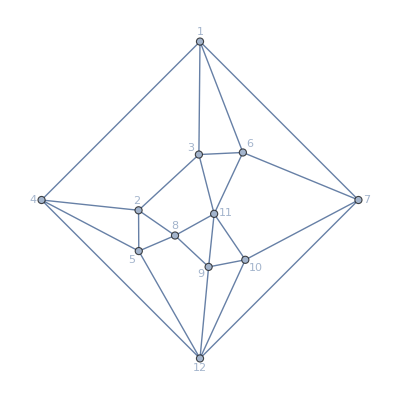
-Graphics-
x[11,12]

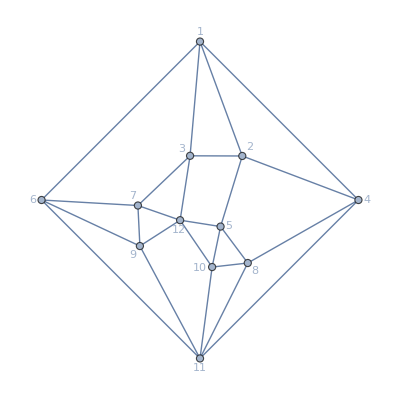
-Graphics-
x[11,12]

```mathematica
fGraphList[8][[163]]//displayfgraph
fGraphList[8][[2521]]//displayfgraph
```

```mathematica
spectrumlist1[9]//DuplicateFreeQ
spectrumlist2[9]//DuplicateFreeQ
spectrumlist3[9]//DuplicateFreeQ
```

$Aborted

False

$Aborted

```mathematica
Select[positionDuplicates[spectrumlist1[9]],Length[#]>1&]
((amplitudeCoefficients[9][[#]]&)/@#)&/@%
Select[positionDuplicates[spectrumlist2[9]],Length[#]>1&]
((amplitudeCoefficients[9][[#]]&)/@#)&/@%
Select[positionDuplicates[spectrumlist3[9]],Length[#]>1&]
((amplitudeCoefficients[9][[#]]&)/@#)&/@%
Intersection[%%%%%%,%%%%,%%]
((amplitudeCoefficients[9][[#]]&)/@#)&/@%
```

{{405,22057},{775,22253},{1672,1745},{2233,32008},{2581,16524},{2970,2971},{2976,35965},{3057,22531},{3789,41776},{4106,31039},{4119,19686},{4509,20754},{4899,16114},{5089,40759},{6129,7257},{6135,6141},{6412,11394},{6516,32718},{6549,23990},{6866,39771},{7220,26740},{8054,11170},{8186,37080},{8222,36982},{8788,38006},{9752,34232},{9753,36806},{9914,18145},{9960,32725},{10268,28195},{10768,31803},{10769,31808},{11008,24559},{11523,11678},{12030,29676},{13418,15407},{13419,14429},{13427,23042},{13704,15422},{13708,14426},{13725,15066},{14330,23912},{14438,23044},{15057,15408},{15070,23043},{15945,22933},{16312,23577},{16401,16407},{16781,18064},{16796,18010},{16913,28971},{17446,19402},{17841,35252},{18550,32824},{18642,18682},{18755,26351},{20734,25636},{20953,39286},{20992,20993},{21072,21082},{21736,21741},{22078,23486},{23294,24758},{23483,32817},{23998,24025},{24658,24660},{24699,24705},{24753,24766},{25018,38129},{25080,33187},{25432,39889},{25646,40262},{25843,40432},{25966,25989},{26311,35229,42248},{28163,42093},{28167,28168},{28309,38554},{28312,38582},{28337,28360},{28344,38574},{28635,29018},{28670,36941},{28766,35838},{28882,34401},{28907,34416},{28931,38576},{29669,39883},{30368,38561},{30858,31113},{31629,39329},{33842,42019},{33926,41215},{33985,34009},{33986,41911},{34296,34354},{34746,34747},{34785,42196},{36221,36326},{36568,42015},{37282,41708},{37283,41709},{37382,42348},{38542,38558},{39878,39974},{39951,39977},{40099,40149},{40245,40275},{40810,40836},{41142,41478},{41584,42450},{41586,42451},{41587,42454},{41588,42455},{41619,42447,42925,43004},{41621,42459},{41892,41893},{41935,41937},{41936,42866},{41938,41939},{42038,42039},{42216,42252},{42219,42251},{42299,42802},{42432,42933},{42449,42929},{42453,42927},{42462,42463},{42478,42482},{42650,42664},{42805,42837},{42812,42813},{42914,42916},{42915,42984},{42917,42980,43015},{42922,42987,43014},{42936,43002},{42963,42964},{42988,42991}}

{{1,0},{0,1},{0,0},{1,0},{-1,0},{0,0},{0,0},{0,0},{0,0},{1,1},{-1,0},{0,0},{0,0},{1,-1},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{1,1},{0,1/2},{0,0},{0,0},{0,0},{0,0},{0,0},{-1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{-1/2,-1/2},{0,0},{0,0},{1,0},{0,0},{0,0},{0,0},{0,0},{0,-1},{0,0},{0,0},{0,-1},{-1/2,0},{0,0},{0,0},{0,0},{0,0},{0,0},{-1,1},{0,0},{0,0},{0,0},{-1/2,0},{0,0},{0,0},{0,0},{0,0},{0,-1},{0,0},{1,0},{0,0},{0,0},{0,0},{0,0},{0,0},{-1,-1},{0,0},{0,0},{0,-1},{0,0},{0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,-1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{-1,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0},{0,0,0},{0,0},{0,0},{0,0}}

{{405,22057},{775,22253},{1672,1745},{2233,32008},{2581,16524},{2970,2971},{2976,35965},{3057,22531},{3789,41776},{4106,31039},{4119,19686},{4509,20754},{4899,16114},{5089,40759},{6129,7257},{6135,6141},{6412,11394},{6516,32718},{6549,23990},{6866,39771},{7220,26740},{8054,11170},{8186,37080},{8222,36982},{8788,38006},{9752,34232},{9753,36806},{9914,18145},{9960,32725},{10268,28195},{10768,31803},{10769,31808},{11008,24559},{11523,11678},{12030,29676},{13418,15407},{13419,14429},{13427,23042},{13704,15422},{13708,14426},{13725,15066},{14330,23912},{14438,23044},{15057,15408},{15070,23043},{15945,22933},{16312,23577},{16401,16407},{16781,18064},{16796,18010},{16913,28971},{17446,19402},{17841,35252},{18550,32824},{18642,18682},{18755,26351},{20734,25636},{20953,39286},{20992,20993},{21072,21082},{21736,21741},{22078,23486},{23294,24758},{23483,32817},{23998,24025},{24658,24660},{24699,24705},{24753,24766},{25018,38129},{25080,33187},{25432,39889},{25646,40262},{25843,40432},{25966,25989},{26311,35229,42248},{28163,42093},{28167,28168},{28309,38554},{28312,38582},{28337,28360},{28344,38574},{28635,29018},{28670,36941},{28766,35838},{28882,34401},{28907,34416},{28931,38576},{29669,39883},{30368,38561},{30858,31113},{31629,39329},{33842,42019},{33926,41215},{33985,34009},{33986,41911},{34296,34354},{34746,34747},{34785,42196},{36221,36326},{36568,42015},{37282,41708},{37283,41709},{37382,42348},{38542,38558},{39878,39974},{39951,39977},{40099,40149},{40245,40275},{40810,40836},{41142,41478},{41584,42450},{41586,42451},{41587,42454},{41588,42455},{41619,42447,42925,43004},{41621,42459},{41892,41893},{41935,41937},{41936,42866},{41938,41939},{42038,42039},{42216,42252},{42219,42251},{42299,42802},{42432,42933},{42449,42929},{42453,42927},{42462,42463},{42478,42482},{42650,42664},{42805,42837},{42812,42813},{42914,42916},{42915,42984},{42917,42980,43015},{42922,42987,43014},{42936,43002},{42963,42964},{42988,42991}}

{{1,0},{0,1},{0,0},{1,0},{-1,0},{0,0},{0,0},{0,0},{0,0},{1,1},{-1,0},{0,0},{0,0},{1,-1},{0,0},{0,0},{0,0},{0,0},{0,0},{1,1},{1,1},{0,1/2},{0,0},{0,0},{0,0},{0,0},{0,0},{-1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{-1/2,-1/2},{0,0},{0,0},{1,0},{0,0},{0,0},{0,0},{0,0},{0,-1},{0,0},{0,0},{0,-1},{-1/2,0},{0,0},{0,0},{0,0},{0,0},{0,0},{-1,1},{0,0},{0,0},{0,0},{-1/2,0},{0,0},{0,0},{0,0},{0,0},{0,-1},{0,0},{1,0},{0,0},{0,0},{0,0},{0,0},{0,0},{-1,-1},{0,0},{0,0},{0,-1},{0,0},{0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,-1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{-1,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0},{0,0,0},{0,0},{0,0},{0,0}}

{{3198,3201},{3295,42292},{3305,30258},{3308,30261},{4704,4860},{4876,25699,25702},{5318,36778},{6135,6141},{7309,16363},{7311,16364},{7661,36799},{7662,36800},{7663,36801},{9752,34232},{9753,36806},{9994,33081},{12642,26436},{16401,16407},{17777,17782},{17789,17793},{20730,26340},{20992,20993},{21072,21082},{21736,21741},{23425,30257},{23487,23493},{23489,23495},{24658,24660},{24699,24705},{26121,35248},{26527,26694},{28167,28168},{32619,34891},{34307,34309},{34746,34747},{36230,36233},{36245,36320},{37282,41708},{37283,41709},{37382,42348},{41584,42450},{41586,42451},{41587,42454},{41588,42455},{41619,42447,42925,43004},{41621,42459},{41892,41893},{41935,41937},{41936,42866},{41938,41939},{42038,42039},{42216,42252},{42219,42251},{42282,42919},{42285,42921},{42299,42802},{42432,42933},{42449,42929},{42453,42927},{42462,42463},{42478,42482},{42805,42837},{42812,42813},{42914,42916},{42915,42984},{42917,42980,43015},{42922,42987,43014},{42936,43002},{42963,42964},{42988,42991}}

{{1,-1},{0,0},{0,0},{-1,1},{-1,1},{0,0,0},{0,0},{0,0},{0,0},{1,-1},{0,0},{-1,1},{0,0},{0,0},{0,0},{0,0},{1,-1},{0,0},{0,0},{-1,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,-1/2},{0,1/2},{0,0},{0,0},{0,0},{-1,1},{0,0},{0,0},{0,0},{0,0},{1,1},{1,-1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0},{0,0,0},{0,0},{0,0},{0,0}}

{{6135,6141},{9752,34232},{9753,36806},{16401,16407},{20992,20993},{21072,21082},{21736,21741},{24658,24660},{24699,24705},{28167,28168},{34746,34747},{37282,41708},{37283,41709},{37382,42348},{41584,42450},{41586,42451},{41587,42454},{41588,42455},{41621,42459},{41892,41893},{41935,41937},{41936,42866},{41938,41939},{42038,42039},{42216,42252},{42219,42251},{42299,42802},{42432,42933},{42449,42929},{42453,42927},{42462,42463},{42478,42482},{42805,42837},{42812,42813},{42914,42916},{42915,42984},{42936,43002},{42963,42964},{42988,42991},{42917,42980,43015},{42922,42987,43014},{41619,42447,42925,43004}}

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0,0},{0,0,0},{0,0,0,0}}

```mathematica
Directory[]
```

C:\Users\qhjm22\OneDrive - Durham University\projects\personal dropbox shared\many_loop_paper\consolidated_multi_loop_data\consolidated_data

```mathematica
Save["spectrum",{spectrumlist1,spectrumlist2,spectrumlist3}]
```

## All graphs related via cusp rule

```mathematica
<<"IGraphM`"
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

```mathematica
myComplement[full_,todel_]:=Fold[Delete[#1,Position[#1,#2,1,1]]&,full,todel]
```

```mathematica
(* vertices of double triangle {v_,w_,v1_,v2_} with v1,v2 left and right (2 valent) v,w top and bottom (3 valent) so v,w merge to 1 vertex in the cusp limit 
Output = {coeffs of all related l loop graphs, coeff of shrunk graph, graph numbers of all related graphs, graph number of shrunk graph. They need to be correctly oriented for it to work...}
 IN: allrelatedfgs[{4,1},{6,7,1,3}]
  OUT: {{1,-1},0,{4,{1,2}},{3,0}}
*)

allrelatedfgs[{loop_,fgn_},{v_,w_,v1_,v2_}]:=Module[{n,fgraph,dials,faces,facesv,facesw,upperfaces,lowerfaces,upperbigface,lowerbigface,newnumeratorpointsupper,newnumeratorpointslower,newedges,newfgraphden,existingnum,existingnumlist,existingnumeratorpointstov,existingnumeratorpointstow,remainignnumerators,allnumeratorpointstovandw,numeratorlist,fgraphs,fgraphscan,fgnums,fgnums1,shrunkgraphs,fgshrunkgnum,coeff,coeffs},n=loop+4;
fgraph=fGraphList[loop][[fgn]];
dials=planarGraphDials[loop][[fnumtodialnum[loop,fgn][[1]]]];
faces=orderedVertsToFaces[dials];
facesv=cycle[#,v]&/@Select[faces,MemberQ[#,v]&];
facesw=cycle[#,w]&/@Select[faces,MemberQ[#,w]&];
upperfaces=Drop[Table[Select[facesv,#[[2]]==vn&][[1]],{vn,cycle[dials[[v]],v1]}],-2];
upperbigface=Join[{v,v1},Flatten[Drop[#,2]&/@upperfaces]];
lowerfaces=Drop[Table[Select[facesw,#[[2]]==wn&][[1]],{wn,cycle[dials[[w]],v2]}],-2];
lowerbigface=Join[{w,v2},Flatten[Drop[#,2]&/@lowerfaces]];
newnumeratorpointsupper=Select[upperbigface,Not[MemberQ[Join[dials[[v]],dials[[w]]],#]]&];
newnumeratorpointslower=Select[lowerbigface,Not[MemberQ[Join[dials[[v]],dials[[w]]],#]]&];
newedges=Join[(x[v,#]&/@newnumeratorpointsupper),(x[w,#]&/@newnumeratorpointslower)];
newfgraphden=Denominator[fgraph]*(Times@@newedges);
existingnum=fGraphNums[loop][[Sequence@@fnumtodialnum[loop,fgn]]];
existingnumlist=({existingnum}/.Times->List)/.a_^b_:>ConstantArray[a,b]//Flatten;
existingnumeratorpointstov=Join[Cases[existingnumlist,x[v,a_]:>a,Infinity],Cases[existingnumlist,x[a_,v]:>a,Infinity]];
existingnumeratorpointstow=Join[Cases[existingnumlist,x[w,a_]:>a,Infinity],Cases[existingnumlist,x[a_,w]:>a,Infinity]];
remainignnumerators=Times@@Select[existingnumlist,Not[MemberQ[#,v]]&&Not[MemberQ[#,w]]&];
allnumeratorpointstovandw=Join[newnumeratorpointsupper,newnumeratorpointslower,existingnumeratorpointstov,existingnumeratorpointstow];
numeratorlist=DeleteDuplicates[(Product[x[v,i],{i,#}]Product[x[w,i],{i,myComplement[allnumeratorpointstovandw,#]}])&/@Subsets[allnumeratorpointstovandw,{Length[newnumeratorpointsupper]+Length[existingnumeratorpointstov]}]/.x[a_,b_]:>x[b,a]/;(b<a)];
fgraphs=(numeratorlist remainignnumerators)/newfgraphden/.x[a_,b_]:>x[b,a]/;(b<a);
fgraphscan=canonicalizefgraph/@fgraphs;
fgnums1=If[#==={},(Print["fgraph not identified: ","loop=",loop," fg number=",fgn," double triangle vertices= ",v,w,v1,v2]);#,#]&/@(Position[fGraphListcan[loop],#]&/@fgraphscan);
fgnums=Flatten[fgnums1];
shrunkgraphs=(fgraphs /.x[a_,b_]:>x[a/.{w->v},b/.{w->v}])(x[v,v]x[v1,v]x[v2,v])/x[v1,v2]/.x[a_,b_]:>x[a/.{n->w},b/.{n->w}]/.x[a_,b_]:>x[b,a]/;a>b;
If[Length[Union[shrunkgraphs]]=!=1,Print["There are different shrunk graphs...",{coeffs,coeff,{loop,fgnums},{loop-1,fgshrunkgnum}}]];
(* Note that the shrunkgraph can also be non valid by having a double denominator term, arising from an edge {x,v} and {x,w} becoming a double edge (not cancelled by any numerator). These clearly have coefficient 0. This is taken care of by the first If statement *)
fgshrunkgnum=If[Cases[Denominator[shrunkgraphs[[1]]],a_^2]=!={},0,If[#==={},0,#[[1,1]]]&@Position[fGraphListcan[loop-1],canonicalizefgraph[shrunkgraphs[[1]]]]];
coeff=If[fgshrunkgnum===0,0,amplitudeCoefficients[loop-1][[fgshrunkgnum]]];
coeffs=amplitudeCoefficients[loop][[fgnums]];
If[Total[coeffs]=!=coeff,Print["Not matching the cusp equation",{coeffs,coeff,{loop,fgnums},{loop-1,fgshrunkgnum}}]];
{coeffs,coeff,{loop,fgnums},{loop-1,fgshrunkgnum}}]
```

```mathematica
detectdoubletriangles[{loop_,fgn_}]:=Module[{fgraph,dials,triangles},fgraph=fGraphList[loop][[fgn]];
dials=planarGraphDials[loop][[fnumtodialnum[loop,fgn][[1]]]];
triangles=Select[orderedVertsToFaces[dials],Length[#]==3&];
Select[Subsets[triangles,{2}],Length[Intersection[#[[1]],#[[2]]]]==2&]]
```

```mathematica
detectnonisomorphicdoubletriangles[{loop_,fgn_}]:=Module[{fgraph,dials,triangles,alldts,dtscurrent,dtsnoniso,autos},
fgraph=fGraphList[loop][[fgn]];
dials=planarGraphDials[loop][[fnumtodialnum[loop,fgn][[1]]]];
triangles=Select[orderedVertsToFaces[dials],Length[#]==3&];
alldts=Select[Subsets[triangles,{2}],Length[Intersection[#[[1]],#[[2]]]]==2&];
autos=graphAutomorphisms[fGraphList[loop][[fgn]]];
dtscurrent=alldts;
dtsnoniso={};
While[Length[dtscurrent]>0,dtsnoniso=Append[dtsnoniso,dtscurrent[[1]]];dtscurrent=Complement[dtscurrent,Table[dtscurrent[[1]]/.ii,{ii,autos}],SameTest->((Sort/@{#1[[1]],#1[[2]]} ==Sort/@{#2[[1]],#2[[2]]})||(Sort/@{#1[[2]],#1[[1]]} ==Sort/@{#2[[1]],#2[[2]]}) &) ]];
dtsnoniso]
```

```mathematica
(* Use FindIsomorphicSubgraph - quicker Outputs directly to {v,w,v1,v2} *)
detectdoubletriangles2[{loop_,fgn_}]:=Module[{fgraph},fgraph=fGraphList[loop][[fgn]];({#[[1,1]],#[[2,2]],#[[1,2]],#[[3,2]]}&)/@EdgeList/@FindIsomorphicSubgraph[(fgraph//displayfgraph)[[1,1]],Graph[{{1,2},{1,3},{2,3},{1,4},{3,4}}],All]]
```

```mathematica
(* NB. This doesn't get orientation right. Need to use dials for that. *) 
detectnonisomorphicdoubletriangles2[{loop_,fgn_}]:=Module[{fgraph,alldts,dtscurrent,dtsnoniso,autos},fgraph=fGraphList[loop][[fgn]];alldts=FindIsomorphicSubgraph[(fgraph//displayfgraph)[[1,1]],Graph[{{1,2},{1,3},{2,3},{1,4},{3,4}}],All];
autos=graphAutomorphisms[fGraphList[loop][[fgn]]];
dtscurrent=alldts;
dtsnoniso={};
While[Length[dtscurrent]>0,dtsnoniso=Append[dtsnoniso,dtscurrent[[1]]];dtscurrent=Complement[dtscurrent,Table[VertexReplace[dtscurrent[[1]],ii],{ii,autos}],SameTest->IGSameGraphQ  ]];
({#[[1,1]],#[[2,2]],#[[1,2]],#[[3,2]]}&)/@EdgeList/@dtsnoniso]
```

```mathematica
detectnonisomorphicdoubletriangles2[{9,1}]
%//Length
doubletriangletovwv1v2/@detectnonisomorphicdoubletriangles[{9,1}]
%//Length
```

{{1,12,10,11},{1,10,12,13},{2,5,4,9},{2,8,4,12},{2,4,5,8},{2,9,5,12},{2,12,8,9},{4,5,2,3},{4,8,2,7},{4,7,3,8},{6,13,3,11},{6,9,5,11},{6,11,9,13},{7,13,3,10},{7,10,8,13},{10,12,1,8},{10,13,1,7}}

17

{doubletriangletovwv1v2[{{1,10,12},{1,12,11}}],doubletriangletovwv1v2[{{1,10,12},{1,13,10}}],doubletriangletovwv1v2[{{1,10,12},{8,12,10}}],doubletriangletovwv1v2[{{1,12,11},{9,11,12}}],doubletriangletovwv1v2[{{2,4,5},{2,5,9}}],doubletriangletovwv1v2[{{2,4,5},{2,8,4}}],doubletriangletovwv1v2[{{2,4,5},{3,5,4}}],doubletriangletovwv1v2[{{2,5,9},{2,9,12}}],doubletriangletovwv1v2[{{2,5,9},{5,6,9}}],doubletriangletovwv1v2[{{2,8,4},{2,12,8}}],doubletriangletovwv1v2[{{2,8,4},{4,8,7}}],doubletriangletovwv1v2[{{2,9,12},{2,12,8}}],doubletriangletovwv1v2[{{2,9,12},{9,11,12}}],doubletriangletovwv1v2[{{2,12,8},{8,12,10}}],doubletriangletovwv1v2[{{4,8,7},{7,8,10}}],doubletriangletovwv1v2[{{6,11,9},{6,13,11}}],doubletriangletovwv1v2[{{6,11,9},{9,11,12}}]}

17

```mathematica
doubletriangletovwv1v2[dt_]:=Module[{tallied=Tally[Flatten[#]]&@dt,vw,dtcycledtov},vw=Select[#,#[[2]]==2&][[All,1]]&@(tallied);dtcycledtov={cycle[dt[[1]],vw[[1]]],cycle[dt[[2]],vw[[1]]]};If[dtcycledtov[[1,2]]!=vw[[2]],{vw[[1]],vw[[2]],dtcycledtov[[2,3]],dtcycledtov[[1,2]]},{vw[[1]],vw[[2]],dtcycledtov[[1,3]],dtcycledtov[[2,2]]}]]
```

```mathematica
allsidewaysrelationstofgraph[{loop_,fgn_}]:=allsidewaysrelationstofgraph[{loop,fgn}]=
Module[{dts=detectnonisomorphicdoubletriangles[{loop,fgn}]},allrelatedfgs[{loop,fgn},doubletriangletovwv1v2[#]]&/@dts]
```

```mathematica
Clear[allsidewaysrelationstofgraph2]
allsidewaysrelationstofgraph2[{loop_,fgn_}]:=allsidewaysrelationstofgraph2[{loop,fgn}]=allrelatedfgs[{loop,fgn},#]&/@detectnonisomorphicdoubletriangles2[{loop,fgn}]
```

```mathematica
detectnonisomorphicdoubletriangles2[{9,4000}]
doubletriangletovwv1v2/@detectnonisomorphicdoubletriangles[{9,4000}]
```

{{1,13,5,9},{1,9,10,13},{2,8,3,9},{2,13,3,9},{2,3,8,13},{2,9,8,13},{3,13,2,11},{4,10,8,12},{4,12,10,11},{5,13,1,6},{5,6,12,13},{6,12,5,7},{6,13,5,7},{6,7,12,13},{7,12,6,11},{7,13,6,11},{7,11,12,13},{8,9,2,10},{8,10,4,9},{9,10,1,8},{9,13,1,2},{11,13,3,7},{11,12,4,7}}

{{1,13,9,5},{5,13,1,6},{1,9,10,13},{9,10,1,8},{13,9,1,2},{2,8,9,3},{2,3,8,13},{2,9,13,8},{8,9,2,10},{2,13,3,9},{13,3,2,11},{13,11,3,7},{4,10,8,12},{10,8,4,9},{4,12,10,11},{11,12,4,7},{5,6,13,12},{6,13,5,7},{12,6,5,7},{6,7,13,12},{7,13,6,11},{12,7,6,11},{7,11,13,12}}

( Import saved data)

```mathematica
SetDirectory[NotebookDirectory[]];
Get["allsidewaysrelationstofgraph.m"]
```

Get::noopen: Cannot open allsidewaysrelationstofgraph.m.

$Failed

```mathematica
highlightgraph[{loop_,fgn_},dt_]:=Column[{HighlightGraph[PlanarGraph[fgraphtograph[fGraphList[loop][[fgn]]],VertexLabels->"Name"],UndirectedEdge@@@Join[Subsets[dt[[1]],{2}],Subsets[dt[[2]],{2}]]],Numerator[fGraphList[loop][[fgn]]]}]
```

```mathematica
highlightalldoubletriangles[{loop_,fgn_}]:=highlightgraph[{loop,fgn},#]&/@detectnonisomorphicdoubletriangles[{loop,fgn}]
```

{{{1},1,{4,{1}},{3,1}},{{1},1,{4,{1}},{3,1}},{{1},1,{4,{1}},{3,1}},{{1,-1},0,{4,{1,2}},{3,0}}}

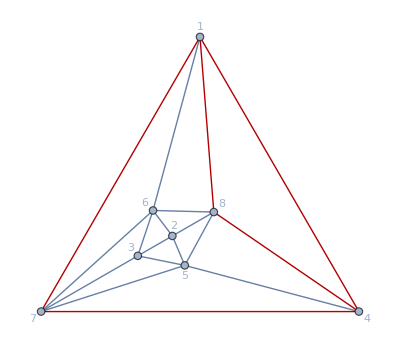
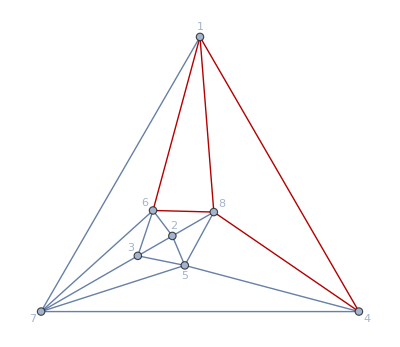
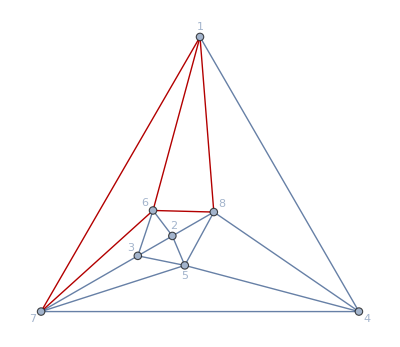
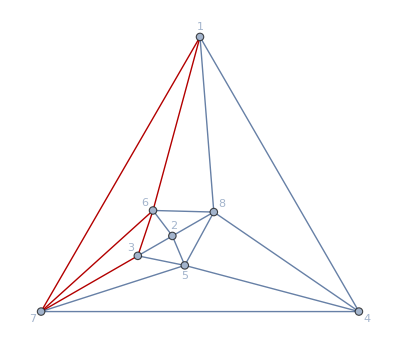
{-Graphics-
x[5,6] x[7,8],-Graphics-
x[5,6] x[7,8],-Graphics-
x[5,6] x[7,8],-Graphics-
x[5,6] x[7,8]}

```mathematica
allsidewaysrelationstofgraph[{4,1}]
highlightalldoubletriangles[{4,1}]
```

{{{0,-1,1},0,{6,{33,32,34}},{5,0}},{{0,0},0,{6,{33,14}},{5,0}}}

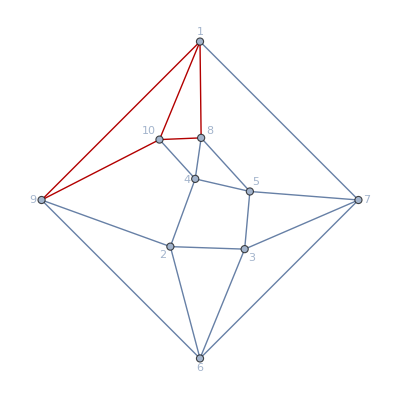
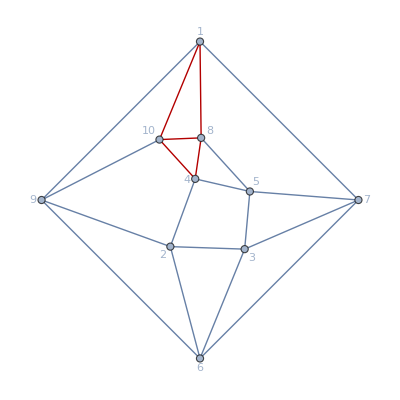
{-Graphics-
1,-Graphics-
1}

```mathematica
allsidewaysrelationstofgraph[{6,33}]
highlightalldoubletriangles[{6,33}]
```

```mathematica
allrelations[loop_]:=allrelations[loop]=Table[allsidewaysrelationstofgraph[{loop,k}],{k,1,Length[fGraphList[loop]]}]
```

```mathematica
Clear[verticalrelations]
verticalrelations[loop_]:=verticalrelations[loop]=Select[Flatten[allrelations[loop],1],#[[2]]=!=0&]//Union
```

```mathematica
Clear[verticallygeneratedfgraphs]
verticallygeneratedfgraphs[loop_]:=verticallygeneratedfgraphs[loop]=Select[verticalrelations[loop],Length[#[[3,2]]]===1&][[All,3,2]]//Flatten//Union
```

```mathematica
verticallygeneratedfgraphs[4]
```

{1,3}

```mathematica
Clear[sidewaysrelationtoverticallygenerated]
```

```mathematica
sidewaysrelationtoverticallygenerated[loop_,0]:=sidewaysrelationtoverticallygenerated[loop,0]=verticallygeneratedfgraphs[loop]
```

```mathematica
sidewaysrelationtoverticallygenerated[loop_,n_]:=sidewaysrelationtoverticallygenerated[loop,n]=Complement@@Join[{Flatten[allrelations[loop][[sidewaysrelationtoverticallygenerated[loop,n-1]]],1][[All,3,2]]//Flatten//Union},Table[sidewaysrelationtoverticallygenerated[loop,kk],{kk,0,n-1}]]
```

```mathematica
sidewaysrelationtoverticallygenerated[4,1]
```

{2}

```mathematica
sidewaysrelationtoverticallygenerated[8,4]
displayfgraph[fGraphList[8][[#]]]&/@%
amplitudeCoefficients[8][[#]]&/@%%
```

$Aborted

$Aborted

$Aborted

```mathematica
Clear[missingfgraphs]
missingfgraphs[loop_]:=missingfgraphs[loop]=Complement[Range[Length[amplitudeCoefficients[loop]]],Union[Flatten[(lvl=0;exp={};While[Length[sidewaysrelationtoverticallygenerated[loop,lvl]]>0,exp=Join[exp,sidewaysrelationtoverticallygenerated[loop,lvl]];lvl++];exp)]]]
```

```mathematica
missingfgraphs[6]
amplitudeCoefficients[6][[#]]&/@missingfgraphs[6]
```

{22,36}

{0,0}

```mathematica
missingfgraphs[7]
amplitudeCoefficients[7][[#]]&/@missingfgraphs[7]
```

{146,201}

{0,0}

```mathematica
missingfgraphs[8]
amplitudeCoefficients[8][[#]]&/@missingfgraphs[8]
```

{929,1569,1570,1719,1720,1796,2327,2337,2345,2376,2378,2382,2383,2665,2686,2705,2707,2708}

{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Length[amplitudeCoefficients[9]]
```

43017

```mathematica
Monitor[allrelations[9],k]
```

$Aborted

```mathematica
SetDirectory[NotebookDirectory[]];
DeleteFile["allsidewaysrelationstofgraph.m"]
Save["allsidewaysrelationstofgraph.m",allsidewaysrelationstofgraph]
```

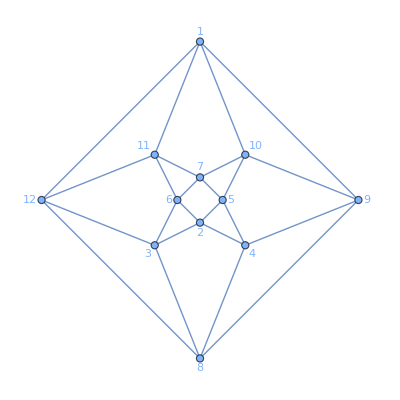
-Graphics-
1

```mathematica
fGraphList[8][[929]]//displayfgraph
```

```mathematica
allrelations8=allrelations[8];
```

```mathematica
Save["allrelations8.m",allrelations8]
```

```mathematica
Count[amplitudeCoefficients[8],0]
```

1649

```mathematica
missingfgraphs[8]
amplitudeCoefficients[8][[#]]&/@missingfgraphs[8]
Length[%]
%-Count[%%,0]
```

{929,1569,1570,1719,1720,1796,2327,2337,2345,2376,2378,2382,2383,2665,2686,2705,2707,2708}

{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

18

1

## generate graphs with pyramids and no numerators (zero coeffs)

```mathematica
loop=6;fgn=14;
fgraph=fGraphList[loop][[fgn]];
edges=Sort/@(Denominator[fgraph]/.Times->List);
numedges={(Numerator[fgraph]/.Power[a_,b_]->a/.Times->List)}//Flatten;
dials=planarGraphDials[loop][[fnumtodialnum[loop,fgn][[1]]]];
fourvalentvertexlist=Position[dials,_?(Length[#]===4&)]//Flatten
pyramidbaselist=Sort/@({x[dials[[#,1]],dials[[#,2]]],x[dials[[#,2]],dials[[#,3]]],x[dials[[#,3]],dials[[#,4]]],x[dials[[#,4]],dials[[#,1]]]})&/@fourvalentvertexlist
diaglist={Sort@x[dials[[#,1]],dials[[#,3]]],Sort@x[dials[[#,2]],dials[[#,4]]]}&/@fourvalentvertexlist
Or@@Table[SubsetQ[edges,pyramidbaselist[[Position[fourvalentvertexlist,ii][[1,1]]]]]&&DisjointQ[numedges,diaglist[[Position[fourvalentvertexlist,ii][[1,1]]]]],{ii,Length[fourvalentvertexlist]}]
Clear[loop,fgn,fgraph,dials,fourvalentvertexlist,faces,edges,tmp,pyramidbaselist,diaglist,pyramidtoplist,numedges]
```

{1,2,3,4,5,6}

{{x[4,6],x[6,10],x[8,10],x[4,8]},{x[3,5],x[5,9],x[7,9],x[3,7]},{x[2,7],x[4,7],x[4,8],x[2,8]},{x[1,8],x[3,8],x[3,7],x[1,7]},{x[2,8],x[8,10],x[9,10],x[2,9]},{x[1,7],x[7,9],x[9,10],x[1,10]}}

{{x[4,10],x[6,8]},{x[3,9],x[5,7]},{x[2,4],x[7,8]},{x[1,3],x[7,8]},{x[2,10],x[8,9]},{x[1,9],x[7,10]}}

False

```mathematica
numeratorfreepyramidQ[loop_,fgn_]:=Module[{fgraph,dials,fourvalentvertexlist,faces,edges,tmp,pyramidbaselist,diaglist,pyramidtoplist,numedges},fgraph=fGraphList[loop][[fgn]];
edges=Sort/@(Denominator[fgraph]/.Times->List);
numedges={(Numerator[fgraph]/.Power[a_,b_]->a/.Times->List)}//Flatten;
dials=planarGraphDials[loop][[fnumtodialnum[loop,fgn][[1]]]];
fourvalentvertexlist=Position[dials,_?(Length[#]===4&)]//Flatten;
pyramidbaselist=Sort/@({x[dials[[#,1]],dials[[#,2]]],x[dials[[#,2]],dials[[#,3]]],x[dials[[#,3]],dials[[#,4]]],x[dials[[#,4]],dials[[#,1]]]})&/@fourvalentvertexlist;
diaglist={Sort@x[dials[[#,1]],dials[[#,3]]],Sort@x[dials[[#,2]],dials[[#,4]]]}&/@fourvalentvertexlist;
Or@@Table[SubsetQ[edges,pyramidbaselist[[Position[fourvalentvertexlist,ii][[1,1]]]]]&&DisjointQ[numedges,diaglist[[Position[fourvalentvertexlist,ii][[1,1]]]]],{ii,Length[fourvalentvertexlist]}]]
```

```mathematica
numeratorfreepyramidQ[6,5]
```

False

```mathematica
Position[Table[numeratorfreepyramidQ[6,ij],{ij,1,Length[fGraphList[6]]}],True]
```

{{1},{10},{20},{22},{23},{26},{35},{36}}

```mathematica
Position[amplitudeCoefficients[6],0]
```

{{1},{10},{14},{20},{22},{23},{26},{33},{35},{36}}

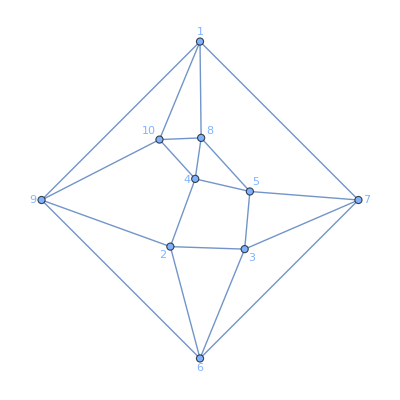

1

```mathematica
PlanarGraph[Denominator[fGraphList[6][[33]]]/.Times->List/.x->List,VertexLabels->"Name"]
Numerator[fGraphList[6][[33]]]
```

## Examine very asymmetric graphs

```mathematica
fGraphList[10][[1]]
```

(x[2,3] x[4,14] x[5,6] x[7,11] x[8,14] x[9,10] x[12,13]^2)/(x[1,10] x[1,11] x[1,13] x[1,14] x[2,4] x[2,5] x[2,7] x[2,8] x[2,13] x[3,4] x[3,5] x[3,6] x[3,9] x[3,14] x[4,5] x[4,8] x[4,9] x[5,13] x[5,14] x[6,9] x[6,11] x[6,12] x[6,14] x[7,8] x[7,10] x[7,12] x[7,13] x[8,9] x[8,12] x[9,12] x[10,11] x[10,12] x[10,13] x[11,12] x[11,14] x[13,14])

```mathematica
(#=!=0&)@3
```

True

11

1

1

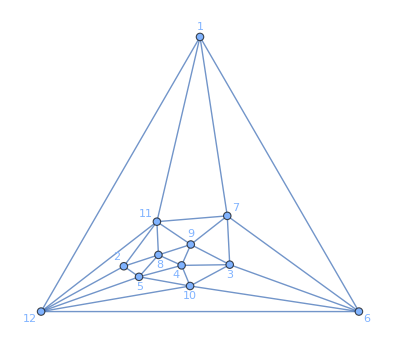
-Graphics-
x[3,11] x[4,6] x[5,9] x[7,12] x[8,12] x[10,11]

{{1,-1,0},0,{8,{11,1425,8}},{7,0}}

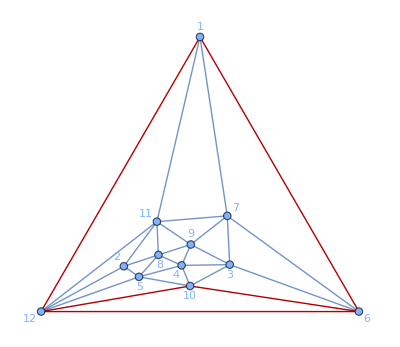
-Graphics-
x[3,11] x[4,6] x[5,9] x[7,12] x[8,12] x[10,11]

{{-1,1,0},0,{8,{1425,11,8}},{7,0}}

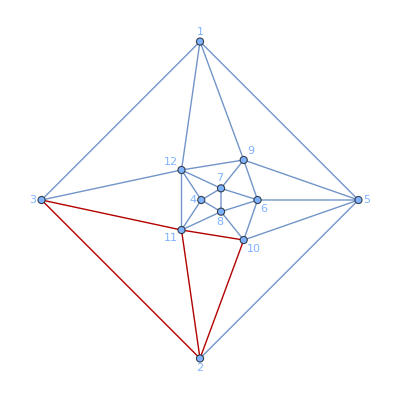
-Graphics-
x[5,12] x[6,11] x[7,11] x[8,9] x[10,12]

{{0,1,-1},0,{8,{8,11,1425}},{7,0}}

-Graphics-
x[3,11] x[4,12] x[5,9] x[6,8] x[7,12] x[10,11]

```mathematica
fp=FirstPosition[amplitudeCoefficients[8],_?(#>0&)][[1]]
amplitudeCoefficients[8][[fp]]
graphSymmetryFactor@(fGraphList[8][[fp]])
fGraphList[8][[fp]]//displayfgraph
allsidewaysrelationstofgraph[{8,fp}][[3]]
highlightalldoubletriangles[{8,fp}][[3]]
allsidewaysrelationstofgraph[{8,1425}][[6]]
highlightalldoubletriangles[{8,1425}][[6]]
allsidewaysrelationstofgraph[{8,8}][[3]]
highlightalldoubletriangles[{8,8}][[3]]
```

```mathematica
collapsecuspreltodenominator[crel_]:=Module[{tmp0,tmp,tmp2,tmp3},tmp0=(fnumtodialnum[crel[[3,1]],#][[1]]&/@(crel[[3,2]]));
tmp={tmp0,crel[[1]]}//Transpose;
tmp2=(Transpose/@Gather[tmp,#1[[1]]===#2[[1]]&]);
tmp3=Transpose[{Union[#[[1]]][[1]],Total[#[[2]]]}&/@tmp2];
ReplacePart[crel,{1->tmp3[[2]],{3,2}->tmp3[[1]]}]]
```

```mathematica
collapsecuspreltodenominator[allrelations[6][[30,8]]]
```

{{1,-2,1},0,{6,{25,27,26}},{5,0}}

```mathematica
allrelationscollpasedtopology[n_]:=allrelationscollpasedtopology[n]=(collapsecuspreltodenominator/@#)&/@allrelations[n]
```

```mathematica
allrelationscollpasedtopology[6]
```

{{{{0},0,{6,{1}},{5,0}},{{0,0},0,{6,{1,8}},{5,0}},{{0,0},0,{6,{1,11}},{5,0}},{{1},1,{6,{1}},{5,3}}},{{{1},1,{6,{1}},{5,1}},{{1},1,{6,{1}},{5,1}},{{1,-1},0,{6,{1,27}},{5,0}},{{1,-1},0,{6,{1,3}},{5,0}},{{1,-1},0,{6,{1,3}},{5,0}},{{1},1,{6,{1}},{5,3}},{{0},0,{6,{1}},{5,0}}},{{{-1},-1,{6,{1}},{5,2}},{{-1,1},0,{6,{1,29}},{5,0}},{{0},0,{6,{1}},{5,0}}},{{{1},1,{6,{2}},{5,3}},{{1},1,{6,{2}},{5,3}},{{1,-1},0,{6,{2,10}},{5,0}},{{1},1,{6,{2}},{5,3}},{{1,0,-1},0,{6,{2,11,3}},{5,0}},{{1},1,{6,{2}},{5,1}},{{1},1,{6,{2}},{5,1}},{{1,-1},0,{6,{2,3}},{5,0}},{{1},1,{6,{2}},{5,1}},{{1},1,{6,{2}},{5,1}},{{1,-1},0,{6,{2,27}},{5,0}},{{1,-2},-1,{6,{2,10}},{5,2}},{{1},1,{6,{2}},{5,4}},{{1,-1},0,{6,{2,10}},{5,0}}},{{{-1},-1,{6,{3}},{5,2}},{{-1},-1,{6,{3}},{5,2}},{{-1,1},0,{6,{3,26}},{5,0}},{{-1},-1,{6,{3}},{5,2}},{{1,-1,0},0,{6,{2,3,11}},{5,0}},{{-1,1},0,{6,{3,1}},{5,0}},{{1,-1},0,{6,{2,3}},{5,0}},{{-1,1},0,{6,{3,1}},{5,0}},{{-1,1},0,{6,{3,29}},{5,0}},{{-1,1},0,{6,{3,5}},{5,0}},{{-1,0},-1,{6,{3,11}},{5,5}}},{{{1},1,{6,{4}},{5,4}},{{1},1,{6,{4}},{5,4}},{{1},1,{6,{4}},{5,4}},{{1,-1},0,{6,{4,23}},{5,0}},{{1},1,{6,{4}},{5,4}},{{1,-1,-1},-1,{6,{4,23,6}},{5,5}},{{1},1,{6,{4}},{5,3}},{{1},1,{6,{4}},{5,3}},{{1},1,{6,{4}},{5,3}},{{1},1,{6,{4}},{5,3}},{{1},1,{6,{4}},{5,3}},{{1},1,{6,{4}},{5,3}},{{1,-1},0,{6,{4,6}},{5,0}},{{1},1,{6,{4}},{5,6}}},{{{1,-1},0,{6,{5,10}},{5,0}},{{1,-1},0,{6,{5,3}},{5,0}},{{1,-1,1},1,{6,{5,10,15}},{5,7}},{{1},1,{6,{5}},{5,7}},{{1},1,{6,{5}},{5,7}},{{1},1,{6,{5}},{5,7}}},{{{-1,1},0,{6,{6,4}},{5,0}},{{-1,1,-1},-1,{6,{6,9,12}},{5,5}},{{-1,1,-1},-1,{6,{6,4,23}},{5,5}},{{-1},-1,{6,{6}},{5,5}},{{-1},-1,{6,{6}},{5,5}},{{-1},-1,{6,{6}},{5,5}},{{-1},-1,{6,{6}},{5,5}}},{{{1},1,{6,{7}},{5,3}},{{1},1,{6,{7}},{5,3}},{{1},1,{6,{7}},{5,3}},{{1},1,{6,{7}},{5,3}},{{1},1,{6,{7}},{5,3}},{{1},1,{6,{7}},{5,3}},{{1,-1},0,{6,{7,20}},{5,0}},{{1,-1,-1},-1,{6,{7,17,27}},{5,5}},{{1},1,{6,{7}},{5,3}},{{1,0,-1},0,{6,{7,8,27}},{5,0}},{{1,-2,-1,0,2},0,{6,{7,20,12,21,13}},{5,0}},{{1},1,{6,{7}},{5,4}},{{1,-1},0,{6,{7,12}},{5,0}}},{{{0},0,{6,{8}},{5,0}},{{0},0,{6,{8}},{5,0}},{{0},0,{6,{8}},{5,0}},{{0},0,{6,{8}},{5,0}},{{0,0},0,{6,{8,30}},{5,0}},{{0,0},0,{6,{1,8}},{5,0}},{{0,0},0,{6,{8,17}},{5,0}},{{1,0,-1},0,{6,{7,8,27}},{5,0}},{{0,1},1,{6,{8,15}},{5,7}},{{0,-1},-1,{6,{8,27}},{5,5}}},{{{1},1,{6,{9}},{5,3}},{{1},1,{6,{9}},{5,3}},{{1,-1},0,{6,{9,10}},{5,0}},{{1},1,{6,{9}},{5,3}},{{1,-1},0,{6,{9,20}},{5,0}},{{1},1,{6,{9}},{5,3}},{{1,-1,-1},-1,{6,{9,12,6}},{5,5}},{{1,-1},0,{6,{9,14}},{5,0}},{{1},1,{6,{9}},{5,1}},{{1},1,{6,{9}},{5,1}},{{1},1,{6,{9}},{5,1}},{{1},1,{6,{9}},{5,1}},{{1,-1,0},0,{6,{9,10,11}},{5,0}}},{{{1},1,{6,{9}},{5,4}},{{1},1,{6,{9}},{5,4}},{{1,-1},0,{6,{9,14}},{5,0}},{{1},1,{6,{9}},{5,4}},{{1,-1},0,{6,{9,23}},{5,0}},{{1},1,{6,{9}},{5,4}},{{1,-1},0,{6,{9,12}},{5,0}},{{1,-1},0,{6,{9,10}},{5,0}},{{1},1,{6,{9}},{5,1}},{{1},1,{6,{9}},{5,1}},{{1},1,{6,{9}},{5,1}},{{1},1,{6,{9}},{5,1}},{{1,-1},0,{6,{9,10}},{5,0}}},{{{-1,1},0,{6,{10,2}},{5,0}},{{-1,1},0,{6,{10,9}},{5,0}},{{-1,1},0,{6,{10,2}},{5,0}},{{-1,1},0,{6,{10,5}},{5,0}},{{1,-1},0,{6,{9,10}},{5,0}},{{-1},-1,{6,{10}},{5,2}},{{-1},-1,{6,{10}},{5,2}},{{-2,1},-1,{6,{10,2}},{5,2}},{{-1,1},0,{6,{10,9}},{5,0}},{{-1},-1,{6,{10}},{5,2}},{{-1},-1,{6,{10}},{5,2}},{{1,-1,0},0,{6,{9,10,11}},{5,0}},{{-1,1,1},1,{6,{10,5,15}},{5,7}},{{-1},-1,{6,{10}},{5,5}},{{-1},-1,{6,{10}},{5,5}},{{-1,1},0,{6,{10,15}},{5,0}},{{-1},-1,{6,{10}},{5,5}},{{-1},-1,{6,{10}},{5,5}},{{-1,1,0},0,{6,{10,15,11}},{5,0}}},{{{0},0,{6,{11}},{5,0}},{{0,-1},-1,{6,{11,27}},{5,5}},{{0,1,-1},0,{6,{11,9,10}},{5,0}},{{-1,0,1},0,{6,{3,11,2}},{5,0}},{{-1,0,1},0,{6,{10,11,15}},{5,0}},{{0,0},0,{6,{11,1}},{5,0}},{{0,-1},-1,{6,{11,3}},{5,5}},{{0,0},0,{6,{11,28}},{5,0}}},{{{-1,1,-1},-1,{6,{12,9,6}},{5,5}},{{-1,1},0,{6,{12,9}},{5,0}},{{-1},-1,{6,{12}},{5,5}},{{-1},-1,{6,{12}},{5,5}},{{-1},-1,{6,{12}},{5,5}},{{-1,1},0,{6,{12,7}},{5,0}},{{-1},-1,{6,{12}},{5,5}},{{-2,-1,2,1,0},0,{6,{20,12,13,7,21}},{5,0}}},{{{2,-2,-1,0,1},0,{6,{13,20,12,21,7}},{5,0}}},{{{-1,1},0,{6,{14,9}},{5,0}},{{-1,1},0,{6,{14,9}},{5,0}},{{-1,1},0,{6,{14,15}},{5,0}},{{-1},-1,{6,{14}},{5,2}},{{-1},-1,{6,{14}},{5,2}},{{-1},-1,{6,{14}},{5,2}}},{{{1,-1,0},0,{6,{15,10,11}},{5,0}},{{1,-1},0,{6,{15,10}},{5,0}},{{1,-1},0,{6,{15,14}},{5,0}},{{1,1,-1},1,{6,{5,15,10}},{5,7}},{{1,0},1,{6,{15,8}},{5,7}}},{{{1},1,{6,{16}},{5,4}},{{1},1,{6,{16}},{5,4}},{{1},1,{6,{16}},{5,4}},{{1},1,{6,{16}},{5,4}},{{1,-1},0,{6,{16,17}},{5,0}}},{{{0},0,{6,{17}},{5,0}},{{0},0,{6,{17}},{5,0}},{{0,0},0,{6,{17,8}},{5,0}},{{-1,1},0,{6,{17,16}},{5,0}}},{{{-1},-1,{6,{17}},{5,5}},{{-1},-1,{6,{17}},{5,5}},{{-1,1,-1},-1,{6,{17,7,27}},{5,5}},{{-1,1},0,{6,{17,16}},{5,0}}},{{{0},0,{6,{18}},{5,0}}},{{{0},0,{6,{19}},{5,0}},{{0},0,{6,{19}},{5,0}},{{0},0,{6,{19}},{5,0}},{{0,0},0,{6,{19,21}},{5,0}},{{1},1,{6,{19}},{5,3}}},{{{1},1,{6,{19}},{5,4}},{{1},1,{6,{19}},{5,4}},{{1},1,{6,{19}},{5,4}},{{1,-1},0,{6,{19,20}},{5,0}},{{1},1,{6,{19}},{5,3}}},{{{-1,1},0,{6,{20,9}},{5,0}},{{-1,1},0,{6,{20,7}},{5,0}},{{-1,1},0,{6,{20,19}},{5,0}},{{-1,-2,2,1,0},0,{6,{12,20,13,7,21}},{5,0}},{{-1},-1,{6,{20}},{5,5}},{{-1},-1,{6,{20}},{5,5}},{{-1},-1,{6,{20}},{5,5}},{{-1},-1,{6,{20}},{5,5}}},{{{0},0,{6,{21}},{5,0}},{{0,0},0,{6,{21,19}},{5,0}},{{0},0,{6,{21}},{5,0}},{{-2,0,2,1,-1},0,{6,{20,21,13,7,12}},{5,0}}},{{{1},1,{6,{22}},{5,6}},{{1},1,{6,{22}},{5,6}},{{1},1,{6,{22}},{5,6}},{{1,-1},0,{6,{22,23}},{5,0}},{{1},1,{6,{22}},{5,4}},{{1},1,{6,{22}},{5,4}},{{1},1,{6,{22}},{5,4}},{{1},1,{6,{22}},{5,4}},{{1},1,{6,{22}},{5,4}}},{{{-1,1},0,{6,{23,4}},{5,0}},{{-1,1},0,{6,{23,22}},{5,0}},{{-1,1},0,{6,{23,9}},{5,0}},{{-1,-1,1},-1,{6,{6,23,4}},{5,5}},{{-1},-1,{6,{23}},{5,5}},{{-1},-1,{6,{23}},{5,5}},{{-1},-1,{6,{23}},{5,5}},{{-1},-1,{6,{23}},{5,5}}},{{{1},1,{6,{24}},{5,6}},{{1},1,{6,{24}},{5,6}}},{{{1},1,{6,{25}},{5,3}},{{1},1,{6,{25}},{5,3}},{{1,-1},0,{6,{25,27}},{5,0}},{{1},1,{6,{25}},{5,4}},{{1},1,{6,{25}},{5,4}},{{1},1,{6,{25}},{5,4}},{{1},1,{6,{25}},{5,4}},{{1,-2,1},0,{6,{25,27,26}},{5,0}}},{{{1,-2,1},0,{6,{26,27,25}},{5,0}},{{1,-1},0,{6,{26,27}},{5,0}},{{1,-1},0,{6,{26,3}},{5,0}}},{{{-1,1},0,{6,{27,2}},{5,0}},{{-1,1},0,{6,{27,1}},{5,0}},{{-1,1},0,{6,{27,25}},{5,0}},{{-1,1,-1},-1,{6,{27,7,17}},{5,5}},{{-1,1,0},0,{6,{27,7,8}},{5,0}},{{-2,1,1},0,{6,{27,26,25}},{5,0}},{{-1},-1,{6,{27}},{5,5}},{{-1},-1,{6,{27}},{5,5}},{{-1,0},-1,{6,{27,11}},{5,5}},{{-1},-1,{6,{27}},{5,5}},{{-1},-1,{6,{27}},{5,5}},{{1,-1,0},0,{6,{29,27,28}},{5,0}},{{-1,1},0,{6,{27,26}},{5,0}},{{-1,0},-1,{6,{27,8}},{5,5}}},{{{0,-1,1},0,{6,{28,27,29}},{5,0}},{{0,0},0,{6,{28,11}},{5,0}}},{{{1,-1},0,{6,{29,1}},{5,0}},{{1,-1},0,{6,{29,3}},{5,0}},{{1,0,-1},0,{6,{29,28,27}},{5,0}},{{1},1,{6,{29}},{5,7}},{{1},1,{6,{29}},{5,7}}},{{{0},0,{6,{30}},{5,0}},{{0},0,{6,{30}},{5,0}},{{0},0,{6,{30}},{5,0}},{{0},0,{6,{30}},{5,0}},{{0,0},0,{6,{30,8}},{5,0}}},{{{0},0,{6,{31}},{5,0}},{{0},0,{6,{31}},{5,0}},{{0},0,{6,{31}},{5,0}}}}

```mathematica
Position[((Length[#[[3,2]]]&)/@#&)/@allrelationscollpasedtopology[6],1]
Position[((Length[#[[3,2]]]&)/@#&)/@allrelations[6],1]
Complement[%%,%]
```

{{1,1},{1,4},{2,1},{2,2},{2,6},{2,7},{3,1},{3,3},{4,1},{4,2},{4,4},{4,6},{4,7},{4,9},{4,10},{4,13},{5,1},{5,2},{5,4},{6,1},{6,2},{6,3},{6,5},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,14},{7,4},{7,5},{7,6},{8,4},{8,5},{8,6},{8,7},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,9},{9,12},{10,1},{10,2},{10,3},{10,4},{11,1},{11,2},{11,4},{11,6},{11,9},{11,10},{11,11},{11,12},{12,1},{12,2},{12,4},{12,6},{12,9},{12,10},{12,11},{12,12},{13,6},{13,7},{13,10},{13,11},{13,14},{13,15},{13,17},{13,18},{14,1},{15,3},{15,4},{15,5},{15,7},{17,4},{17,5},{17,6},{19,1},{19,2},{19,3},{19,4},{20,1},{20,2},{21,1},{21,2},{22,1},{23,1},{23,2},{23,3},{23,5},{24,1},{24,2},{24,3},{24,5},{25,5},{25,6},{25,7},{25,8},{26,1},{26,3},{27,1},{27,2},{27,3},{27,5},{27,6},{27,7},{27,8},{27,9},{28,5},{28,6},{28,7},{28,8},{29,1},{29,2},{30,1},{30,2},{30,4},{30,5},{30,6},{30,7},{32,7},{32,8},{32,10},{32,11},{34,4},{34,5},{35,1},{35,2},{35,3},{35,4},{36,1},{36,2},{36,3}}

{{1,1},{2,1},{2,2},{3,1},{4,1},{4,2},{4,4},{4,6},{4,7},{4,9},{4,10},{4,13},{5,1},{5,2},{5,4},{6,1},{6,2},{6,3},{6,5},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,14},{7,4},{7,5},{7,6},{8,4},{8,5},{8,6},{8,7},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,9},{9,12},{10,1},{10,2},{10,3},{10,4},{11,1},{11,2},{11,4},{11,6},{11,9},{11,10},{11,11},{11,12},{12,1},{12,2},{12,4},{12,6},{12,9},{12,10},{12,11},{12,12},{13,6},{13,7},{13,10},{13,11},{13,14},{13,15},{13,17},{13,18},{14,1},{15,3},{15,4},{15,5},{15,7},{17,4},{17,5},{17,6},{19,1},{19,2},{19,3},{19,4},{20,1},{20,2},{21,1},{21,2},{22,1},{23,1},{23,2},{23,3},{24,1},{24,2},{24,3},{25,5},{25,6},{25,7},{25,8},{26,1},{26,3},{27,1},{27,2},{27,3},{27,5},{27,6},{27,7},{27,8},{27,9},{28,5},{28,6},{28,7},{28,8},{29,1},{29,2},{30,1},{30,2},{30,4},{30,5},{30,6},{30,7},{32,7},{32,8},{32,10},{32,11},{34,4},{34,5},{35,1},{35,2},{35,3},{35,4},{36,1},{36,2},{36,3}}

{{1,4},{2,6},{2,7},{3,3},{23,5},{24,5}}

```mathematica
allsidewaysrelationstofgraph[{6,1}][[4]]
allsidewaysrelationstofgraph[{6,2}][[6]]
allsidewaysrelationstofgraph[{6,2}][[7]]
allsidewaysrelationstofgraph[{6,3}][[3]]
allsidewaysrelationstofgraph[{6,23}][[5]]
allsidewaysrelationstofgraph[{6,24}][[5]]
```

{{0,1},1,{6,{1,2}},{5,3}}

{{1,0},1,{6,{2,1}},{5,3}}

{{1,-1},0,{6,{2,3}},{5,0}}

{{-1,1},0,{6,{3,2}},{5,0}}

{{0,1},1,{6,{23,24}},{5,3}}

{{1,0},1,{6,{24,23}},{5,3}}

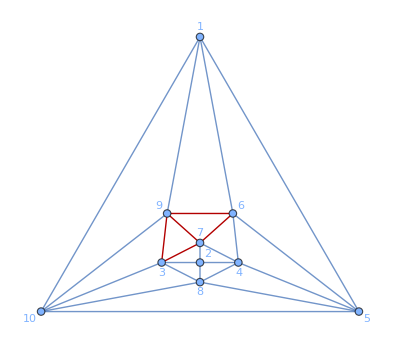
{0,-Graphics-
x[3,6] x[4,10] x[5,7] x[8,9]}

{1,-Graphics-
x[3,6] x[4,10] x[5,9] x[7,8]}

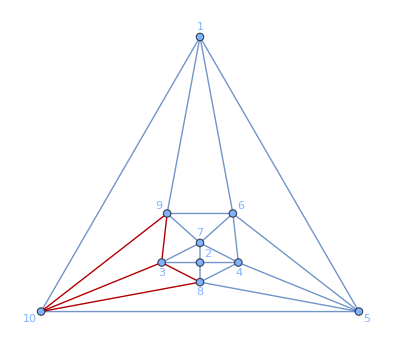
{1,-Graphics-
x[3,6] x[4,10] x[5,9] x[7,8]}

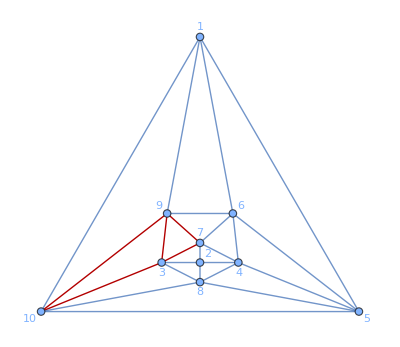
{-1,-Graphics-
x[3,4] x[5,9] x[6,10] x[7,8]}

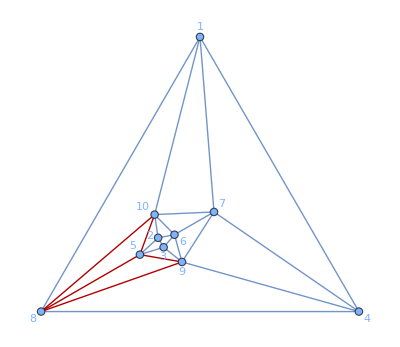
{0,-Graphics-
x[5,7] x[6,8] x[9,10]^2}

{1,-Graphics-
x[5,6] x[7,8] x[9,10]^2}

```mathematica
{amplitudeCoefficients[6][[1]],highlightalldoubletriangles[{6,1}][[4]]}
{amplitudeCoefficients[6][[2]],highlightalldoubletriangles[{6,2}][[6]]}
{amplitudeCoefficients[6][[2]],highlightalldoubletriangles[{6,2}][[7]]}
{amplitudeCoefficients[6][[3]],highlightalldoubletriangles[{6,3}][[3]]}
{amplitudeCoefficients[6][[23]],highlightalldoubletriangles[{6,23}][[5]]}
{amplitudeCoefficients[6][[24]],highlightalldoubletriangles[{6,24}][[5]]}
```

```mathematica
Position[((Length[#[[3,2]]]&)/@#&)/@allrelationscollpasedtopology[7],1];
Position[((Length[#[[3,2]]]&)/@#&)/@allrelations[7],1];
Complement[%%,%]
```

{{1,22},{1,25},{1,27},{2,17},{2,22},{2,25},{2,27},{3,11},{3,12},{3,16},{4,10},{4,11},{4,14},{5,9},{6,3},{6,9},{7,3},{7,9},{8,22},{9,15},{9,22},{10,15},{10,20},{38,16},{39,16},{43,7},{47,27},{48,27},{50,22},{51,22},{52,6},{53,9},{62,14},{63,14},{68,24},{68,25},{69,5},{69,13},{70,5},{71,12},{71,13},{71,14},{72,12},{72,14},{73,12},{73,14},{74,12},{74,14},{76,22},{77,22},{83,9},{84,4},{87,11},{87,14},{88,11},{88,14},{89,12},{89,13},{90,8},{90,9},{104,8},{105,4},{105,5},{106,1},{106,4},{107,5},{114,7},{115,7},{126,10},{127,10},{169,4},{194,3},{195,3},{204,12},{209,9},{210,9}}

```mathematica
allsidewaysrelationstofgraph[{7,1}][[25]]
```

{{1,0},1,{7,{1,2}},{6,9}}

```mathematica
allrelations[4]
```

{{{{1},1,{4,{1}},{3,1}},{{1},1,{4,{1}},{3,1}},{{1},1,{4,{1}},{3,1}},{{1,-1},0,{4,{1,2}},{3,0}}},{{{-1,1},0,{4,{2,1}},{3,0}}},{{{1},1,{4,{3}},{3,1}},{{1},1,{4,{3}},{3,1}}}}

836817

1/(x[1,11] x[1,12] x[1,13] x[1,14] x[2,3] x[2,4] x[2,5] x[2,8] x[3,4] x[3,6] x[3,7] x[4,5] x[4,6] x[5,8] x[5,9] x[6,7] x[6,10] x[7,10] x[7,12] x[8,9] x[8,11] x[9,11] x[9,14] x[10,12] x[10,13] x[11,14] x[12,13] x[13,14])

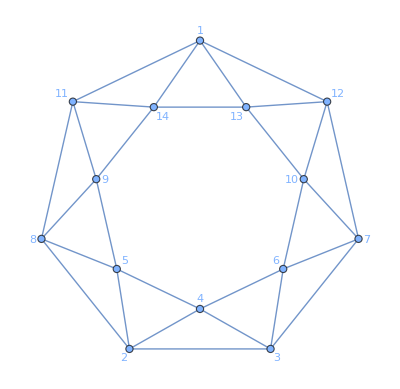
-Graphics-
1

```mathematica
fp=Position[amplitudeCoefficients[10],14][[1,1]]
fGraphList[10][[fp]]
%//displayfgraph
```

## Playing with new rules

```mathematica
(* Use FindIsomorphicSubgraph - quicker Outputs directly to {v,w,v1,v2} *)
detecttripletriangles[{loop_,fgn_}]:=Module[{fgraph},fgraph=fGraphList[loop][[fgn]];FindIsomorphicSubgraph[(fgraph//displayfgraph)[[1,1]],Graph[{{1,2},{1,3},{1,4},{1,5},{2,3},{3,4},{4,5}}],All]]
```

```mathematica
Clear[detectnonisomorphicsquares]
detectnonisomorphicsquares[{loop_,fgn_}]:=Module[{verts,alldts,autos,dtscurrent,dtsnoniso},

verts=Select[orderedVertsToFaces[planarGraphDials[loop][[fnumtodialnum[loop,fgn][[1]]]]],Length[#]==4&];
alldts=Subgraph[displayfgraph[fGraphList[loop][[fgn]]][[1,1]],#]&/@verts;
autos=graphAutomorphisms[fGraphList[loop][[fgn]]];
dtscurrent=alldts;
dtsnoniso={};
While[Length[dtscurrent]>0,dtsnoniso=Append[dtsnoniso,dtscurrent[[1]]];dtscurrent=Complement[dtscurrent,Table[VertexReplace[dtscurrent[[1]],ii],{ii,autos}],SameTest->IGSameGraphQ  ]];
dtsnoniso

]
```

```mathematica
(* NB. This doesn't get orientation right. Need to use dials for that. *) 
Clear[detectnonisomorphicdoubletriangles2]
detectnonisomorphicdoubletriangles2[{loop_,fgn_}]:=Module[{fgraph,alldts,dtscurrent,dtsnoniso,autos},fgraph=fGraphList[loop][[fgn]];alldts=FindIsomorphicSubgraph[(fgraph//displayfgraph)[[1,1]],Graph[{{1,2},{1,3},{2,3},{1,4},{3,4}}],All];
autos=graphAutomorphisms[fGraphList[loop][[fgn]]];
dtscurrent=alldts;
dtsnoniso={};
While[Length[dtscurrent]>0,dtsnoniso=Append[dtsnoniso,dtscurrent[[1]]];dtscurrent=Complement[dtscurrent,Table[VertexReplace[dtscurrent[[1]],ii],{ii,autos}],SameTest->IGSameGraphQ  ]];
dtsnoniso]
```

```mathematica
detectnonisomorphictripletriangles[{loop_,fgn_}]:=Module[{fgraph,alldts,dtscurrent,dtsnoniso,autos},fgraph=fGraphList[loop][[fgn]];alldts=FindIsomorphicSubgraph[(fgraph//displayfgraph)[[1,1]],Graph[{{1,2},{1,3},{1,4},{1,5},{2,3},{3,4},{4,5}}],All];
autos=graphAutomorphisms[fGraphList[loop][[fgn]]];
dtscurrent=alldts;
dtsnoniso={};
While[Length[dtscurrent]>0,dtsnoniso=Append[dtsnoniso,dtscurrent[[1]]];dtscurrent=Complement[dtscurrent,Table[VertexReplace[dtscurrent[[1]],ii],{ii,autos}],SameTest->IGSameGraphQ  ]];
dtsnoniso]
```

```mathematica
detectnonisomorphicdoubledoubletrianglesbarv3is4valent[{loop_,fgn_}]:=Module[{fgraph,alldts,dtscurrent,dtsnoniso,autos,allsgisos,allgoodsgisos},

fgraph=fGraphList[loop][[fgn]];
allsgisos=FindSubgraphIsomorphism[Graph[{{1,2},{2,3},{3,4},{4,5},{6,1},{6,2},{6,3},{7,3},{7,4},{7,5},{6,7}}],(fgraph//displayfgraph)[[1,1]],All];
(* Select those subgraphs for which v3 is 4 valent (so does not appear in the numerator) and there is no edge {v2,v4}  *)
allgoodsgisos=Select[allsgisos,(Not[MemberQ[Cases[{Numerator[fgraph]},x[a_,b_]->{a,b},Infinity]//Flatten//Union,3/.#]]&&Intersection[Denominator[fgraph]/.Times->List,{x[2/.#,4/.#],x[4/.#,2/.#]}]==={})&];
alldts=VertexReplace[Graph[{{1,2},{2,3},{3,4},{4,5},{6,1},{6,2},{6,3},{7,3},{7,4},{7,5},{6,7}}],#/.Association->List,VertexLabels->"Name"]&/@allgoodsgisos;
autos=graphAutomorphisms[fGraphList[loop][[fgn]]];
dtscurrent=alldts;
dtsnoniso={};
While[Length[dtscurrent]>0,dtsnoniso=Append[dtsnoniso,dtscurrent[[1]]];dtscurrent=Complement[dtscurrent,Table[VertexReplace[dtscurrent[[1]],ii],{ii,autos}],SameTest->IGSameGraphQ  ]];
dtsnoniso]
```

```mathematica
detectallnonisomorphicsubshapes[{loop_,fgn_},subgraphfaces_]:=Module[{subgraph,fgraph,fgraphgraph,alldts,dtscurrent,dtsnoniso,autos,allsgisos,allgoodsgisos},
subgraph=Graph[Union[Sort/@Flatten[Partition[#,2, 1, {1,1}]&/@subgraphfaces,1]]];
fgraph=fGraphList[loop][[fgn]];
fgraphgraph=(fgraph//displayfgraph)[[1,1]];
allsgisos=FindSubgraphIsomorphism[subgraph,fgraphgraph,All];
(* Select those   for which  the subgraph is "on the surface" so it's faces are faces of the fgraph *)
allgoodsgisos=Select[allsgisos,(SubsetQ[Sort/@PlanarFaceList[fgraphgraph],Sort/@(subgraphfaces/.#)])&];
alldts=VertexReplace[subgraph,#/.Association->List,VertexLabels->"Name"]&/@allgoodsgisos;
autos=graphAutomorphisms[fGraphList[loop][[fgn]]];
dtscurrent=alldts;
dtsnoniso={};
While[Length[dtscurrent]>0,dtsnoniso=Append[dtsnoniso,dtscurrent[[1]]];dtscurrent=Complement[dtscurrent,Table[VertexReplace[dtscurrent[[1]],ii],{ii,autos}],SameTest->IGSameGraphQ  ]];
dtsnoniso]
```

```mathematica
(* Double triangle *)
rung[{l_,fgn_},{v0_,v1_,v2_,v3_}]:=((fGraphList[l][[fgn]]x[v0,v2]/.(x[a_,b_]:>x[a/.{v2->l+5},b/.{v2->l+5}])) x[v1,v3])/(x[v1,v2]x[v2,v3]x[v2,l+5]x[v0,v2])/.x[a_,b_]:>x[b,a]/;b<a
(* Square *)
rung2[{l_,fgn_},{v1_,v2_,v3_,v4_}]:=((fGraphList[l][[fgn]])x[v1,v3]x[v2,v4])/(x[v1,l+5]x[v2,l+5]x[v3,l+5]x[v4,l+5])/.x[a_,b_]:>x[b,a]/;b<a
```

```mathematica
(* Triple triangle *)

-Graphics-

superrung[{l_,fgn_},{v0_,v1_,v2_,v3_,v4_}]:=((fGraphList[l][[fgn]]x[v0,v2]x[v0,v3]/.(x[a_,b_]:>x[a/.{v2->l+5,v3->l+6},b/.{v2->l+5,v3->l+6}])) x[v1,v4])/(x[v1,v2]x[v2,v3]x[v3,v4]x[v2,l+5]x[v3,l+6]x[v0,v2]x[v0,v3])/.x[a_,b_]:>x[b,a]/;b<a
```

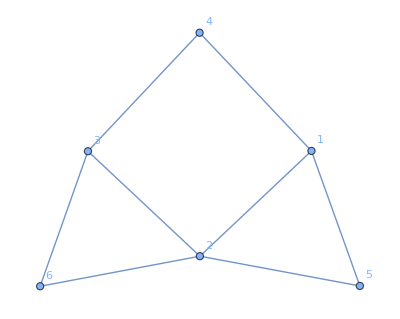

```mathematica
Graph[Union[Sort/@Flatten[Partition[#,2, 1, {1,1}]&/@#,1]],VertexLabels->"Name"]&@{{1,2,3,4},{2,1,5},{3,2,6}}
```

```mathematica
(* Square triangle triangle*)
-Graphics-;

squaretriangletrianglethread[{l_,fgn_},{v1_,v2_,v3_,v4_,v5_,v6_}]:=fGraphList[l][[fgn]]x[v3,v2]x[v1,v2]x[v5,v6]/(x[v2,l+5]x[v1,l+5]x[v2,l+6]x[v3,l+6]x[v5,l+5]x[l+5,l+6]x[l+6,v6])/.x[a_,b_]:>x[b,a]/;b<a
```

```mathematica
-Graphics-;
superrung2[{l_,fgn_},{v1_,v2_,v3_,v4_,v5_,v6_,v7_}]:=((fGraphList[l][[fgn]]x[v2,v6]x[v4,v7]/.(x[a_,b_]:>x[a/.{v2->l+5,v4->l+6},b/.{v2->l+5,v4->l+6}])) x[v1,v5]x[v3,l+5]x[v3,l+6])/(x[v1,v2]x[v2,v3]x[v3,v4]x[v4,v5]x[v2,l+5]x[v4,l+6]x[v6,v2]x[v4,v7]x[l+5,l+6])/.x[a_,b_]:>x[b,a]/;b<a
```

```mathematica
runggenerate[{l_,fgn_}]:=Module[{tts,ttvertices,fgs,out},tts=detectnonisomorphicdoubletriangles2[{l,fgn}];
ttvertices=({1,2,3,4}/.FindGraphIsomorphism[Graph[{{1,2},{1,3},{1,4},{2,3},{3,4}}],#])[[1]]&/@tts;
fgs=canonicalizefgraph/@(rung[{l,fgn},#]&/@ttvertices);
out={{l,{fgn,amplitudeCoefficients[l][[fgn]]}},{l+1,Transpose[({#,amplitudeCoefficients[l+1][[#]]})&/@(Position[fGraphListcan[l+1],#][[1,1]]&/@fgs)]}};
If[{out[[1,2,2]]}==Union[out[[2,2,2]]],out,Print["rung coefficient mismatch at ",l," loops, Graph number ",fgn,". Output = ",out]];out
]
```

```mathematica
rung2generate[{l_,fgn_}]:=Module[{tts,ttvertices,fgs,out},tts=detectnonisomorphicsquares[{l,fgn}];
ttvertices=({1,2,3,4}/.FindGraphIsomorphism[Graph[{{1,2},{2,3},{3,4},{4,1}}],#])[[1]]&/@tts;
fgs=canonicalizefgraph/@(rung2[{l,fgn},#]&/@ttvertices);
out=If[tts==={},{{l,{fgn,amplitudeCoefficients[l][[fgn]]}},{l+1,{{},{}}}},{{l,{fgn,amplitudeCoefficients[l][[fgn]]}},{l+1,Transpose[({#,amplitudeCoefficients[l+1][[#]]})&/@(Position[fGraphListcan[l+1],#][[1,1]]&/@fgs)]}}];
If[({out[[1,2,2]]}==Union[out[[2,2,2]]])||(out[[2,2,1]]==={}),out,Print["rung coefficient mismatch at ",l," loops, Graph number ",fgn,". Output = ",out]]
]
```

```mathematica
superrunggenerate[{l_,fgn_}]:=Module[{tts,ttvertices,fgs,out},tts=detectnonisomorphictripletriangles[{l,fgn}];
ttvertices=({1,2,3,4,5}/.FindGraphIsomorphism[Graph[{{1,2},{1,3},{1,4},{1,5},{2,3},{3,4},{4,5}}],#])[[1]]&/@tts;
fgs=canonicalizefgraph/@(superrung[{l,fgn},#]&/@ttvertices);
out=If[tts==={},{{l,{fgn,amplitudeCoefficients[l][[fgn]]}},{l+2,{{},{}}}},{{l,{fgn,amplitudeCoefficients[l][[fgn]]}},{l+2,Transpose[({#,amplitudeCoefficients[l+2][[#]]})&/@(Position[fGraphListcan[l+2],#][[1,1]]&/@fgs)]}}];
If[({-out[[1,2,2]]}==Union[out[[2,2,2]]])||(out[[2,2,1]]==={}),out,Print["superrung coefficient mismatch at ",l," loops, Graph number ",fgn,". Output = ",out]]
]
```

```mathematica
squaretriangletrianglethreadgenerate[{l_,fgn_}]:=Module[{tts,ttvertices,fgs,out},tts=detectallnonisomorphicsubshapes[{l,fgn},{{1,2,3,4},{2,1,5},{3,2,6}}];
ttvertices=({1,2,3,4,5,6}/.FindGraphIsomorphism[-Graphics-,#])[[1]]&/@tts;
fgs=canonicalizefgraph/@(squaretriangletrianglethread[{l,fgn},#]&/@ttvertices);
out=If[tts==={},{{l,{fgn,amplitudeCoefficients[l][[fgn]]}},{l+2,{{},{}}}},{{l,{fgn,amplitudeCoefficients[l][[fgn]]}},{l+2,Transpose[({#,amplitudeCoefficients[l+2][[#]]})&/@(Position[fGraphListcan[l+2],#][[1,1]]&/@fgs)]}}];
If[({-2out[[1,2,2]]}==Union[out[[2,2,2]]])||(out[[2,2,1]]==={}),out,Print["squaretriangle coefficient mismatch at ",l," loops, Graph number ",fgn,". Output = ",out];out]
]
```

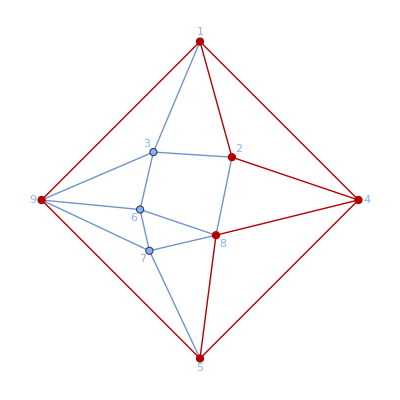
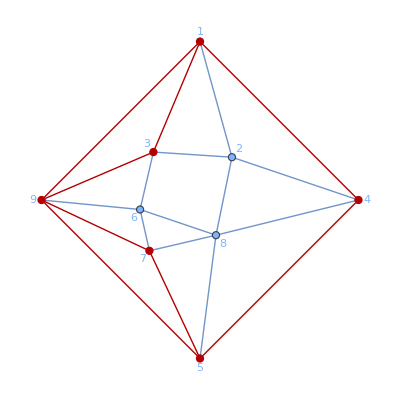
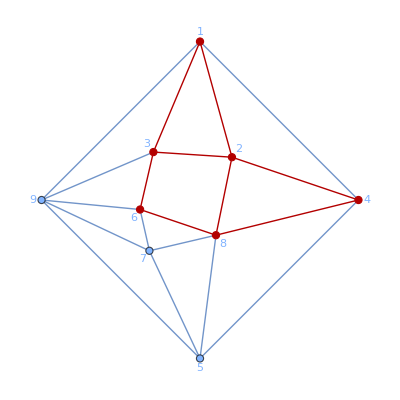
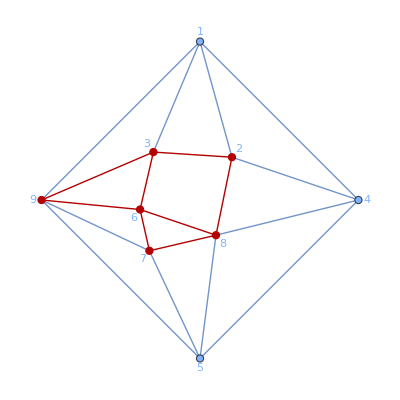

```mathematica
detectallnonisomorphicsubshapes[{5,5},{{1,2,3,4},{2,1,5},{3,2,6}}];
HighlightGraph[displayfgraph[fGraphList[5][[5]]][[1,1]],#]&/@%
```

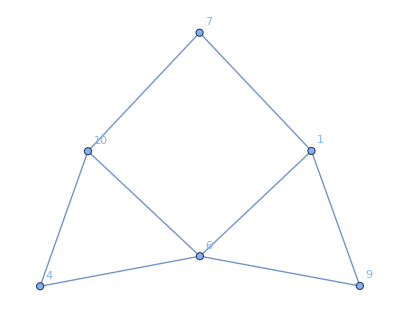
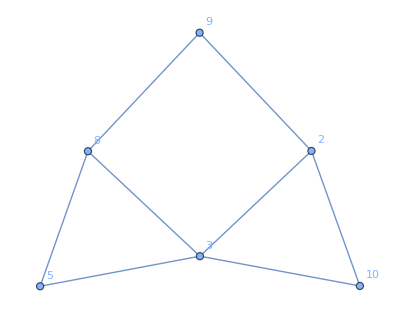
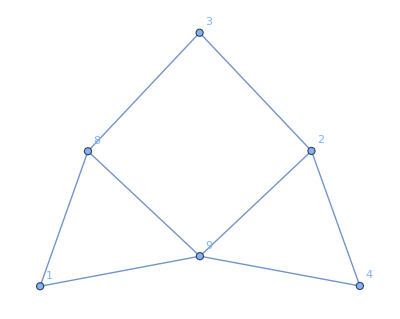
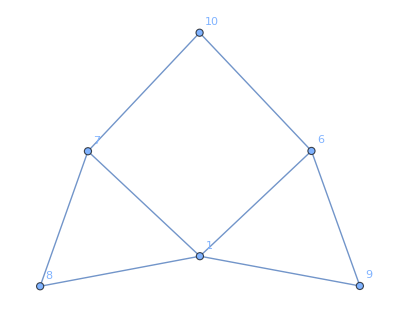
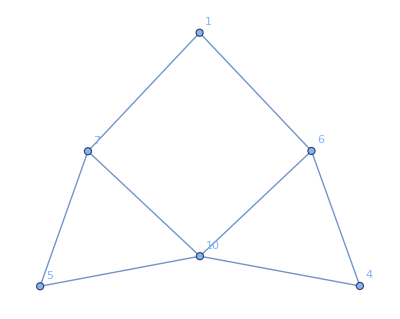

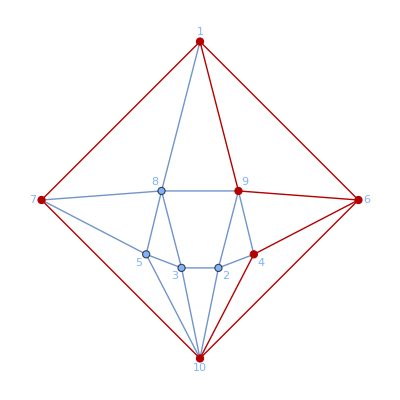
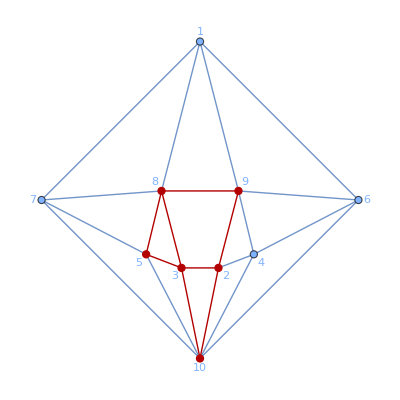
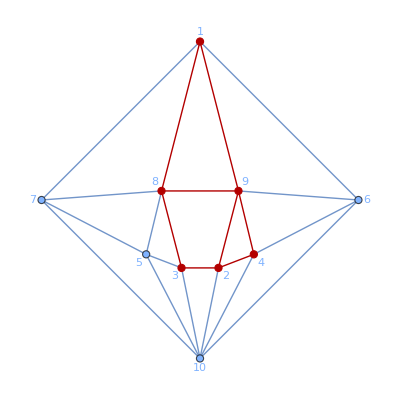

```mathematica
detectallnonisomorphicsubshapes[{6,8},{{1,2,3,4},{2,1,5},{3,2,6}}];
HighlightGraph[displayfgraph[fGraphList[6][[8]]][[1,1]],#]&/@%
```

```mathematica
squaretriangletrianglethreadgenerate[{4,2}]
```

{{4,{2,-1}},{6,{{16},{2}}}}

```mathematica
superrung2generate[{l_,fgn_}]:=Module[{tts,ttvertices,fgs,out},tts=detectnonisomorphicdoubledoubletrianglesbarv3is4valent[{l,fgn}];
ttvertices=({1,2,3,4,5,6,7}/.FindGraphIsomorphism[Graph[{{1,2},{2,3},{3,4},{4,5},{6,1},{6,2},{6,3},{7,3},{7,4},{7,5},{6,7}}],#])[[1]]&/@tts;
fgs=canonicalizefgraph/@(superrung2[{l,fgn},#]&/@ttvertices);
out=If[tts==={},{{l,{fgn,amplitudeCoefficients[l][[fgn]]}},{l+2,{{},{}}}},{{l,{fgn,amplitudeCoefficients[l][[fgn]]}},{l+2,Transpose[({#,amplitudeCoefficients[l+2][[#]]})&/@(Position[fGraphListcan[l+2],#][[1,1]]&/@fgs)]}}];
If[({-2out[[1,2,2]]}==Union[out[[2,2,2]]])||(out[[2,2,1]]==={}),out,Print["superrung coefficient mismatch at ",l," loops, Graph number ",fgn,". Output = ",out]]
]
```

```mathematica
superrung2generate[{5,#}]&/@Range[7]
```

superrung coefficient mismatch at 5 loops, Graph number 2. Output = {{5,{2,-1}},{7,{{104},{1}}}}

superrung coefficient mismatch at 5 loops, Graph number 5. Output = {{5,{5,-1}},{7,{{37,104,138},{0,1,2}}}}

{{{5,{1,1}},{7,{{},{}}}},Null,{{5,{3,1}},{7,{{},{}}}},{{5,{4,1}},{7,{{},{}}}},Null,{{5,{6,1}},{7,{{},{}}}},{{5,{7,1}},{7,{{},{}}}}}

```mathematica
allrunggenerated[l_]:=(runggenerate[{l,#}][[2,2,1]]&)/@Range[Length[amplitudeCoefficients[l]]]
```

```mathematica
allrung2generated[l_]:=(rung2generate[{l,#}][[2,2,1]]&)/@Range[Length[amplitudeCoefficients[l]]]
```

```mathematica
allsuperrunggenerated[l_]:=(superrunggenerate[{l,#}][[2,2,1]]&)/@Range[Length[amplitudeCoefficients[l]]]
allsquaretriangletrianglethreadgenerated[l_]:=(squaretriangletrianglethreadgenerate[{l,#}][[2,2,1]]&)/@Range[Length[amplitudeCoefficients[l]]]
```

```mathematica
Monitor[Table[squaretriangletrianglethreadgenerate[{7,i}],{i,1,10}],i]
```

squaretriangle coefficient mismatch at 7 loops, Graph number 8. Output = {{7,{8,-1}},{9,{{10648,17440,10654,17440},{1,1,1,1}}}}

{{{7,{1,1}},{9,{{},{}}}},{{7,{2,0}},{9,{{},{}}}},{{7,{3,-1}},{9,{{},{}}}},{{7,{4,1}},{9,{{},{}}}},{{7,{5,1}},{9,{{},{}}}},{{7,{6,0}},{9,{{},{}}}},{{7,{7,0}},{9,{{},{}}}},{{7,{8,-1}},{9,{{10648,17440,10654,17440},{1,1,1,1}}}},{{7,{9,0}},{9,{{10649,17439,10653,17441},{0,0,0,0}}}},{{7,{10,0}},{9,{{10651,17444,10650,17443},{0,0,0,0}}}}}

```mathematica
Length[fGraphList[7]]
```

```mathematica
generatedbyrungrules[l_]:=Union[Flatten[{allrunggenerated[l-1],allrunggenerated[l-1],allsuperrunggenerated[l-2]}]]
```

```mathematica
allsquaretriangletrianglethreadgenerated[4]
{{allsquaretriangletrianglethreadgenerated[5]}, {allsquaretriangletrianglethreadgenerated[6]}}
```

{{},{16},{}}

squaretriangle coefficient mismatch at 5 loops, Graph number 2. Output = {{5,{2,-1}},{7,{{104},{1}}}}

squaretriangle coefficient mismatch at 5 loops, Graph number 5. Output = {{5,{5,-1}},{7,{{138,104,138,214},{2,1,2,1}}}}

squaretriangle coefficient mismatch at 5 loops, Graph number 7. Output = {{5,{7,1}},{7,{{162,21},{-1,-1}}}}

squaretriangle coefficient mismatch at 6 loops, Graph number 5. Output = {{6,{5,-1}},{8,{{1906,2215,612},{1,1,1}}}}

squaretriangle coefficient mismatch at 6 loops, Graph number 7. Output = {{6,{7,1}},{8,{{249,292,76,279,2307,2669,75},{-1,-1,-1,-1,-1,-1,-1}}}}

squaretriangle coefficient mismatch at 6 loops, Graph number 8. Output = {{6,{8,-1}},{8,{{684,2242,1661,302,779},{1,1,1,2,0}}}}

squaretriangle coefficient mismatch at 6 loops, Graph number 13. Output = {{6,{13,-1}},{8,{{1768,2215,220,2597},{1,1,1,1}}}}

squaretriangle coefficient mismatch at 6 loops, Graph number 15. Output = {{6,{15,-1}},{8,{{2571,103,1623,1830},{2,1,1,1}}}}

squaretriangle coefficient mismatch at 6 loops, Graph number 17. Output = {{6,{17,-1}},{8,{{145},{1}}}}

squaretriangle coefficient mismatch at 6 loops, Graph number 18. Output = {{6,{18,1}},{8,{{1730,122,1757,76,198,2564},{-1,-1,-1,-1,-1,-1}}}}

squaretriangle coefficient mismatch at 6 loops, Graph number 21. Output = {{6,{21,-1}},{8,{{1661,2391},{1,1}}}}

squaretriangle coefficient mismatch at 6 loops, Graph number 25. Output = {{6,{25,-1}},{8,{{2556,612,2556,2597},{2,1,2,1}}}}

squaretriangle coefficient mismatch at 6 loops, Graph number 28. Output = {{6,{28,-1}},{8,{{1788,1809,1788,145},{2,1,2,1}}}}

squaretriangle coefficient mismatch at 6 loops, Graph number 31. Output = {{6,{31,1}},{8,{{2122,127,2122},{-2,-1,-2}}}}

squaretriangle coefficient mismatch at 6 loops, Graph number 32. Output = {{6,{32,-1}},{8,{{2469,2614,2469,145,103,135,2469,2123},{2,1,2,1,1,1,2,1}}}}

squaretriangle coefficient mismatch at 6 loops, Graph number 34. Output = {{6,{34,1}},{8,{{2479,1907,117},{-1,-1,-1}}}}

{{{{},{104},{},{},{138,104,138,214},{},{162,21}}},{{{},{},{},{},{1906,2215,612},{},{249,292,76,279,2307,2669,75},{684,2242,1661,302,779},{},{70,655},{},{},{1768,2215,220,2597},{2598,197,1742,779},{2571,103,1623,1830},{},{145},{1730,122,1757,76,198,2564},{},{1660,2390},{1661,2391},{},{},{},{2556,612,2556,2597},{1201,2581},{},{1788,1809,1788,145},{},{},{2122,127,2122},{2469,2614,2469,145,103,135,2469,2123},{261,1739},{2479,1907,117},{2624,1238,1174,2279},{2297,2281}}}}

#### Examine Cusp relations with many terms in

```mathematica
((Length[#[[1]]])&/@#)&/@allrelations[8];
%//Flatten//Union
Position[%%,14]
allrelations[8][[#[[1]],#[[2]]]]&/@%
```

{1,2,3,4,5,6,7,8,10,11,14,20}

{{203,13},{1917,9},{1923,4},{2122,3},{2123,12},{2124,15},{2150,4},{2154,7},{2403,8},{2405,16},{2406,18},{2407,9},{2413,20},{2414,14},{2434,19},{2435,16},{2468,17},{2469,8},{2700,1}}

{{{1,2,1,-2,0,-1,0,-1,0,1,-1,0,-1,1},0,{8,{2123,2469,203,2122,2413,2405,2124,2434,2435,2407,2414,2406,2468,2403}},{7,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0},0,{8,{1924,2367,2702,1922,1917,2154,1923,2150,2154,2700,2367,1924,1922,2702}},{7,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0},0,{8,{2154,1922,1923,2700,2367,1917,2150,1924,2702,2154,1924,2702,1922,2367}},{7,0}},{{-2,1,1,0,1,-1,0,0,2,-1,-1,0,-1,1},0,{8,{2122,2407,203,2124,2123,2405,2406,2435,2469,2434,2468,2413,2414,2403}},{7,0}},{{0,1,-2,-1,1,0,1,0,0,-1,2,1,-1,-1},0,{8,{2124,2123,2122,2405,2407,2406,203,2413,2435,2414,2469,2403,2434,2468}},{7,0}},{{1,0,-2,-1,0,1,1,0,-1,2,0,1,-1,-1},0,{8,{2123,2124,2122,2405,2406,203,2407,2413,2414,2469,2435,2403,2434,2468}},{7,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0},0,{8,{2154,2702,2150,2700,1924,1917,1923,2367,1922,2154,2367,1922,2702,1924}},{7,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0},0,{8,{2150,2702,2154,2700,2367,1917,2154,1924,1922,1923,2367,2702,1922,1924}},{7,0}},{{1,-1,-1,0,-1,1,1,-1,0,2,0,1,0,-2},0,{8,{2403,2468,2434,2406,2405,203,2407,2414,2413,2469,2435,2123,2124,2122}},{7,0}},{{-1,0,0,2,-1,1,1,0,1,-2,1,-1,-1,0},0,{8,{2434,2413,2435,2469,2405,2407,203,2124,2123,2122,2403,2468,2414,2406}},{7,0}},{{-1,-1,2,0,1,1,-2,1,-1,0,0,-1,1,0},0,{8,{2468,2414,2469,2406,203,2123,2122,2403,2434,2413,2435,2405,2407,2124}},{7,0}},{{0,0,-1,1,0,-1,2,1,-2,1,1,-1,0,-1},0,{8,{2413,2124,2405,2123,2435,2434,2469,2407,2122,203,2403,2414,2406,2468}},{7,0}},{{-1,-1,1,1,0,0,2,0,1,-2,1,-1,0,-1},0,{8,{2434,2405,2407,203,2413,2435,2469,2124,2123,2122,2403,2468,2406,2414}},{7,0}},{{-1,0,1,-1,2,1,-2,1,-1,-1,1,0,0,0},0,{8,{2468,2406,203,2414,2469,2123,2122,2403,2434,2405,2407,2413,2435,2124}},{7,0}},{{-1,0,0,1,-1,1,1,0,2,-2,1,0,-1,-1},0,{8,{2405,2413,2124,2123,2434,2407,203,2435,2469,2122,2403,2406,2414,2468}},{7,0}},{{2,0,-2,0,-1,1,0,-1,-1,1,1,1,-1,0},0,{8,{2469,2435,2122,2413,2414,2123,2124,2434,2468,203,2407,2403,2405,2406}},{7,0}},{{-1,0,1,-1,2,1,-2,1,0,-1,0,-1,0,1},0,{8,{2434,2435,2407,2468,2469,203,2122,2403,2413,2405,2124,2414,2406,2123}},{7,0}},{{1,1,2,-2,0,-1,-1,-1,0,0,-1,1,0,1},0,{8,{2123,203,2469,2122,2406,2414,2468,2405,2413,2124,2434,2407,2435,2403}},{7,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0},0,{8,{2700,1922,2702,1922,1923,2154,1924,2702,2154,2150,2367,1924,2367,1917}},{7,0}}}

```mathematica
allsidewaysrelationstofgraph[{8,2700}]
```

{{{0,0,0,0,0,0,0,0,0,0,0,0,0,0},0,{8,{2700,1922,2702,1922,1923,2154,1924,2702,2154,2150,2367,1924,2367,1917}},{7,0}},{{0},0,{8,{2700}},{7,0}}}

```mathematica
fnumtodialnum[8,3]
```

{1,3}

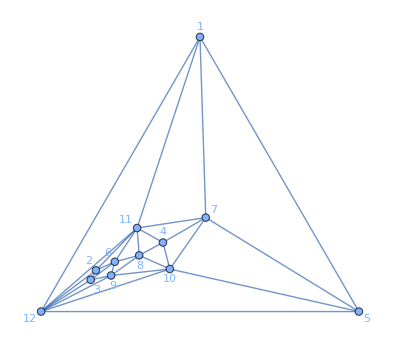
-Graphics-
x[6,12] x[7,12] x[8,12] x[9,11] x[10,11]^2

```mathematica
fGraphListcan[8][[2403]]//displayfgraph
```

{{1,-1,-1,0,-1,1,1,-1,0,2,0,1,0,-2},0,{8,{2403,2468,2434,2406,2405,203,2407,2414,2413,2469,2435,2123,2124,2122}},{7,0}}

{x[6,12] x[7,12] x[8,12] x[9,11] x[10,11]^2,x[8,12] x[9,12] x[10,11]^2,x[7,12] x[8,11] x[9,11] x[10,12],x[8,12] x[9,12] x[10,11]^2,x[7,12] x[8,11] x[9,11] x[10,12],x[9,12] x[10,11],x[8,12] x[9,12] x[10,11],x[8,12] x[9,12] x[10,11]^2,x[7,12] x[8,11] x[9,11] x[10,12],x[9,12] x[10,11],x[8,12] x[9,12] x[10,11],x[9,11] x[10,12],x[8,12] x[9,12] x[10,11],x[11,12]}

{d^6,d^4,d^4,d^4,d^4,d^2,d^3,d^4,d^4,d^2,d^3,d^2,d^3,d}

{{1,12,11},{2,11,12}}

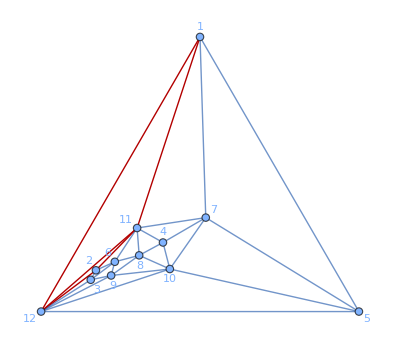
-Graphics-
x[6,12] x[7,12] x[8,12] x[9,11] x[10,11]^2

```mathematica
allsidewaysrelationstofgraph[{8,2403}][[8]]
fGraphNums[8][[Sequence@@fnumtodialnum[8,#]]]&/@(%[[3,2]])
%/.x[_,_]->d
detectnonisomorphicdoubletriangles[{8,2403}][[8]]
highlightalldoubletriangles[{8,2403}][[8]]
```

```mathematica
allrelations[8][[All,All,]]
```

```mathematica
allrunggenerated[4]
allrung2generated[4]
allsuperrunggenerated[3]
```

{{3,4,4,1},{5},{4,6}}

{{},{2},{}}

{{5,2}}

```mathematica
allsuperrunggenerated[6]
```

{{1298,1098,1089,729,772,735},{1301,1299,1096,1093,731,774,734,1097,1090,733,730,770},{1302,1094,732,773},{613,622,615,614,623,624,786,788,836,837,882,789,834,883,1122,1141,1143,1883,1882,1125,1140,1884,1422,1425,1422},{584,1220,625,1300,750,839,854,756,775,862,902,855,1113,1151,1147,1886,1889,750},{681,681,281,1991,2228,2246,2246,2228,321,317,1677,1676,371,1622,278,666,303,296,2088,1842,2045,432,1883,1842,371},{2143,2310,1999,2669,2240,2441},{1625,311,1990,2242,684,685,1992,373,1678,1844,1888},{654,1197,1952,1979,1197,654,2405,2415,1218,515,819,1854,1842,999,597,490,266,242,1143,1435,1006,387,1842,190},{655,1184,1982,1974,2416,992,593,243,492,268,1219,518,820,1855,1847,1440,1013},{1620,214,210,256,2595,2569,2457,2460,433,83,1006,2088,2076,1158,1592,1908,1731,1745,2209,730,836,1471,921,1509},{1621,215,211,257,2596,2570,2458,2461,432,81,1007,2089,2077,1157,1593,1909,1732,1746,2212,733,837,1473,921,1510},{255,2462,2577,2597,2491,2466,195,247,251,194,616,2217,854,85,1009,435,2102,2082,1147,1889,1596,1753,1734,96,438,1016,2071,2097,750,1429,845,1474,922,1517},{585,2467,250,754,860,1017,2083,97,440,2099},{1980,202,1623,258,203,260,1844,823,1010,1599},{2122},{216,2563,2496,1886,1753,1760,1477,839,1522,926},{259,1981,2495,857,1843},{2389,2389,1775,2077,371,1698},{2390,2387,1773,2079,372},{2391,2388,1774,2081,373},{2175},{2554,2120,579,2572,2557,793,1556},{2555,2121,580,2573,2558,795,1557},{2116,2407,1202,659,2418,2123,1913,247,584,2563},{2124,2118,1201,2115,581,2562},{1790,339,2658,1807,1807,1798,276,1783,1791,1746,2494,2558,1706},{277,340,2660,2661,1805,1809,1799,2496,1758,2563},{1811,1791},{2610,2414,2414,2507,2520,580,2487,2494,2039,1509,2104,1909,2494},{2504,2524,1527},{1975,2501,2523,2418,2123,2517,2503,2522,2617,1010,1911,1514,1526,1220,2466,584,2491,2496,493,251},{2525},{2526,2615,1152,2493,2499,842},{2288,2624,2629,2279,2289,2631},{2636,2281,2632}}

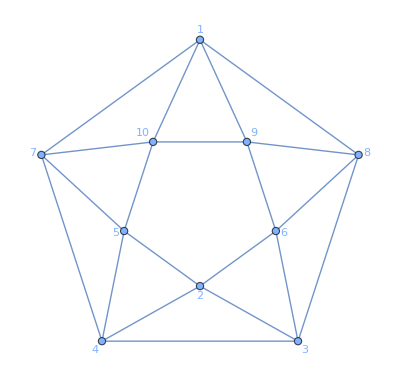
-Graphics-
1

```mathematica
displayfgraph@fGraphList[6][[16]]
```

{{{-1,1},0,{4,{2,1}},{3,0}}}

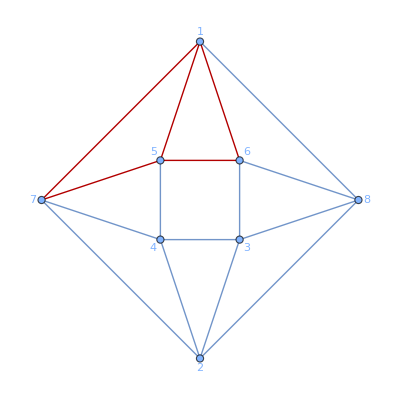
{-Graphics-
1}

```mathematica
allsidewaysrelationstofgraph[{4,2}]
highlightalldoubletriangles[{4,2}]
```

{{{2,-1,-1,0,-1,1},0,{6,{16,25,15,26,25,9}},{5,0}}}

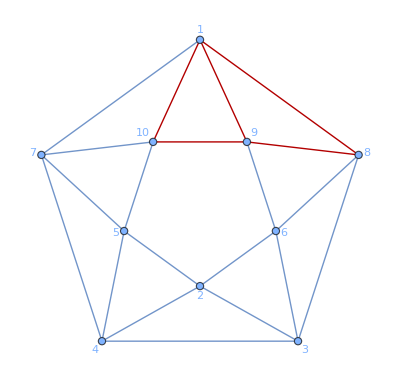
{-Graphics-
1}

16 | {{{2,-1,-1,0,-1,1},0,{6,{16,25,15,26,25,9}},{5,0}}}
25 | {{{-1,1},0,{6,{25,11}},{5,0}},{{-1,1},0,{6,{25,9}},{5,0}},{{-1,1},0,{6,{25,24}},{5,0}},{{-1,-1,2,1,-1,0},0,{6,{15,25,16,9,25,26}},{5,0}},{{-1},-1,{6,{25}},{5,5}},{{-1},-1,{6,{25}},{5,5}},{{-1},-1,{6,{25}},{5,5}},{{-1},-1,{6,{25}},{5,5}}}
15 | {{{-1,1,-1},-1,{6,{15,11,8}},{5,5}},{{-1,1},0,{6,{15,12}},{5,0}},{{-1},-1,{6,{15}},{5,5}},{{-1},-1,{6,{15}},{5,5}},{{-1},-1,{6,{15}},{5,5}},{{-1,1},0,{6,{15,9}},{5,0}},{{-1},-1,{6,{15}},{5,5}},{{-1,-1,2,1,0,-1},0,{6,{25,15,16,9,26,25}},{5,0}}}
26 | {{{0},0,{6,{26}},{5,0}},{{0,0},0,{6,{26,23}},{5,0}},{{0},0,{6,{26}},{5,0}},{{-1,0,2,1,-1,-1},0,{6,{25,26,16,9,15,25}},{5,0}}}
25 | {{{-1,1},0,{6,{25,11}},{5,0}},{{-1,1},0,{6,{25,9}},{5,0}},{{-1,1},0,{6,{25,24}},{5,0}},{{-1,-1,2,1,-1,0},0,{6,{15,25,16,9,25,26}},{5,0}},{{-1},-1,{6,{25}},{5,5}},{{-1},-1,{6,{25}},{5,5}},{{-1},-1,{6,{25}},{5,5}},{{-1},-1,{6,{25}},{5,5}}}
9 | {{{1},1,{6,{9}},{5,3}},{{1},1,{6,{9}},{5,3}},{{1},1,{6,{9}},{5,3}},{{1},1,{6,{9}},{5,3}},{{1},1,{6,{9}},{5,3}},{{1},1,{6,{9}},{5,3}},{{1,-1},0,{6,{9,25}},{5,0}},{{1,-1,-1},-1,{6,{9,21,32}},{5,5}},{{1},1,{6,{9}},{5,3}},{{1,0,-1},0,{6,{9,10,32}},{5,0}},{{1,-1,-1,0,-1,2},0,{6,{9,25,15,26,25,16}},{5,0}},{{1},1,{6,{9}},{5,4}},{{1,-1},0,{6,{9,15}},{5,0}}}

{{{-1,1},0,{5,{5,1}},{4,0}},{{-1,1},0,{5,{5,3}},{4,0}},{{-1,1},0,{5,{5,4}},{4,0}},{{-1,-1,1},-1,{5,{5,5,3}},{4,2}},{{-1},-1,{5,{5}},{4,2}},{{-1},-1,{5,{5}},{4,2}}}

```mathematica
allsidewaysrelationstofgraph[{6,16}]
highlightalldoubletriangles[{6,16}]
Grid[{#,allsidewaysrelationstofgraph[{6,#}]}&/@(%%[[1,3,2]])]
allsidewaysrelationstofgraph[{5,5}]
```

```mathematica
Join[#,Complement[{5,2,4,3},#]]&/@Subsets[{5,2,4,3},{2}]
```

{{5,2,3,4},{5,4,2,3},{5,3,2,4},{2,4,3,5},{2,3,4,5},{4,3,2,5}}

```mathematica
allsidewaysrelationstofgraph[{6,16}]
highlightalldoubletriangles[{6,16}]
((x[9,#[[1]]]x[9,#[[2]]]x[1,#[[3]]]x[1,#[[4]]]&)/@(Join[#,Complement[{5,2,4,3},#]]&/@Subsets[{5,2,4,3},{2}]))/(x[9,5]x[9,2]x[1,4]x[1,3])
Position[fGraphListcan[6],#]&/@(canonicalizefgraph/@(fGraphList[6][[16]]((x[9,#[[1]]]x[9,#[[2]]]x[1,#[[3]]]x[1,#[[4]]]&)/@(Join[#,Complement[{5,2,4,3},#]]&/@Subsets[{5,2,4,3},{2}]))/(x[9,5]x[9,2]x[1,4]x[1,3])))//Flatten
amplitudeCoefficients[6][[#]]&/@%
```

{{{2,-1,-1,0,-1,1},0,{6,{16,25,15,26,25,9}},{5,0}}}

{-Graphics-
1}

{1,(x[1,2] x[9,4])/(x[1,4] x[9,2]),(x[1,2] x[9,3])/(x[1,3] x[9,2]),(x[1,5] x[9,4])/(x[1,4] x[9,5]),(x[1,5] x[9,3])/(x[1,3] x[9,5]),(x[1,2] x[1,5] x[9,3] x[9,4])/(x[1,3] x[1,4] x[9,2] x[9,5])}

{16,26,25,25,15,9}

{2,0,-1,-1,-1,1}

{{{-5,2,1,2,0,1,1,-1,-1,0,0,0,2,0,-1,-1,0,0,-1,1},0,{8,{1609,2556,1623,2571,1201,1202,1623,1197,1181,1188,1608,1201,2556,1179,1180,1181,1200,1179,1197,1176}},{7,0}}}

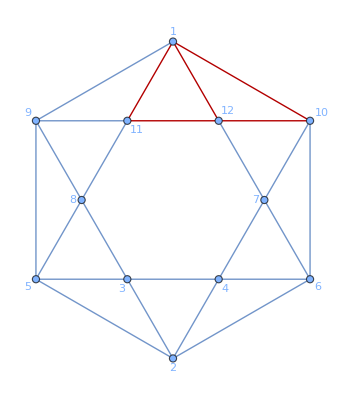
{-Graphics-
1}

{{8,3,4,2,5,6},{8,3,5,2,4,6},{8,3,2,4,5,6},{8,3,6,2,4,5},{8,4,5,2,3,6},{8,4,2,3,5,6},{8,4,6,2,3,5},{8,5,2,3,4,6},{8,5,6,2,3,4},{8,2,6,3,4,5},{3,4,5,2,6,8},{3,4,2,5,6,8},{3,4,6,2,5,8},{3,5,2,4,6,8},{3,5,6,2,4,8},{3,2,6,4,5,8},{4,5,2,3,6,8},{4,5,6,2,3,8},{4,2,6,3,5,8},{5,2,6,3,4,8}}

{1,(x[1,4] x[12,5])/(x[1,5] x[12,4]),(x[1,4] x[12,2])/(x[1,2] x[12,4]),(x[1,4] x[12,6])/(x[1,6] x[12,4]),(x[1,3] x[12,5])/(x[1,5] x[12,3]),(x[1,3] x[12,2])/(x[1,2] x[12,3]),(x[1,3] x[12,6])/(x[1,6] x[12,3]),(x[1,3] x[1,4] x[12,2] x[12,5])/(x[1,2] x[1,5] x[12,3] x[12,4]),(x[1,3] x[1,4] x[12,5] x[12,6])/(x[1,5] x[1,6] x[12,3] x[12,4]),(x[1,3] x[1,4] x[12,2] x[12,6])/(x[1,2] x[1,6] x[12,3] x[12,4]),(x[1,8] x[12,5])/(x[1,5] x[12,8]),(x[1,8] x[12,2])/(x[1,2] x[12,8]),(x[1,8] x[12,6])/(x[1,6] x[12,8]),(x[1,4] x[1,8] x[12,2] x[12,5])/(x[1,2] x[1,5] x[12,4] x[12,8]),(x[1,4] x[1,8] x[12,5] x[12,6])/(x[1,5] x[1,6] x[12,4] x[12,8]),(x[1,4] x[1,8] x[12,2] x[12,6])/(x[1,2] x[1,6] x[12,4] x[12,8]),(x[1,3] x[1,8] x[12,2] x[12,5])/(x[1,2] x[1,5] x[12,3] x[12,8]),(x[1,3] x[1,8] x[12,5] x[12,6])/(x[1,5] x[1,6] x[12,3] x[12,8]),(x[1,3] x[1,8] x[12,2] x[12,6])/(x[1,2] x[1,6] x[12,3] x[12,8]),(x[1,3] x[1,4] x[1,8] x[12,2] x[12,5] x[12,6])/(x[1,2] x[1,5] x[1,6] x[12,3] x[12,4] x[12,8])}

{1609,1608,1201,2556,1201,1202,1623,1200,1179,1197,2556,1623,2571,1179,1180,1181,1197,1181,1188,1176}

{-5,0,0,2,0,1,1,0,0,-1,2,1,2,0,-1,-1,-1,-1,0,1}

```mathematica
allsidewaysrelationstofgraph[{8,1609}]
highlightalldoubletriangles[{8,1609}]
(Join[#,Complement[{8,3,4,5,2,6},#]]&/@Subsets[{8,3,4,5,2,6},{3}])
((x[12,#[[1]]]x[12,#[[2]]]x[12,#[[3]]]x[1,#[[4]]]x[1,#[[5]]]x[1,#[[6]]]&)/@(Join[#,Complement[{8,3,4,5,2,6},#]]&/@Subsets[{8,3,4,5,2,6},{3}]))/(x[12,8]x[12,3]x[12,4]x[1,5]x[1,2]x[1,6])
Position[fGraphListcan[8],#]&/@(canonicalizefgraph/@(fGraphList[8][[1609]]((x[12,#[[1]]]x[12,#[[2]]]x[12,#[[3]]]x[1,#[[4]]]x[1,#[[5]]]x[1,#[[6]]]&)/@(Join[#,Complement[{8,3,4,5,2,6},#]]&/@Subsets[{8,3,4,5,2,6},{3}]))/(x[12,8]x[12,3]x[12,4]x[1,5]x[1,2]x[1,6])))//Flatten
amplitudeCoefficients[8][[#]]&/@%
```

1/(x[1,9] x[1,10] x[1,11] x[1,12] x[2,3] x[2,4] x[2,5] x[2,6] x[3,4] x[3,5] x[3,8] x[4,6] x[4,7] x[5,8] x[5,9] x[6,7] x[6,10] x[7,10] x[7,12] x[8,9] x[8,11] x[9,11] x[10,12] x[11,12])

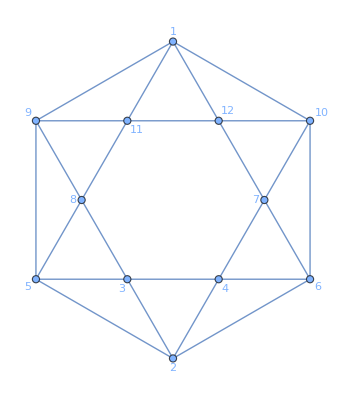
-Graphics-
1

{{-1.83697×10^-16,1.},{6.12323×10^-17,-1.},{-0.288675,-0.5},{0.288675,-0.5},{-0.866025,-0.5},{0.866025,-0.5},{0.57735,-8.9407×10^-8},{-0.57735,-1.78814×10^-7},{-0.866025,0.5},{0.866025,0.5},{-0.288675,0.5},{0.288675,0.5}}

{{{1609}},{{2564}},{{1757}},{{261}},{{1608}},{{1623}},{{2564}},{{1597}},{{245}},{{246}},{{1623}},{{1624}},{{1757}},{{1598}},{{246}},{{421}},{{1606}},{{1597}},{{1598}},{{1595}}}

{1609,2564,1757,261,1608,1623,2564,1597,245,246,1623,1624,1757,1598,246,421,1606,1597,1598,1595}

{-5,-1,-1,0,0,1,-1,0,0,0,1,0,-1,0,0,0,0,0,0,0}

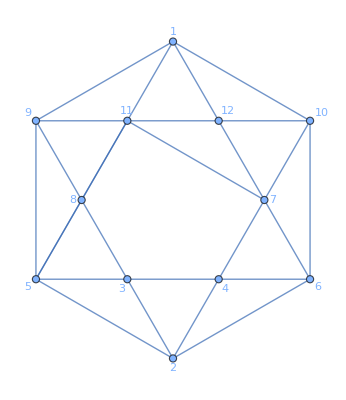
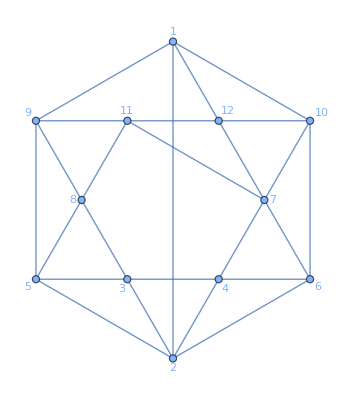
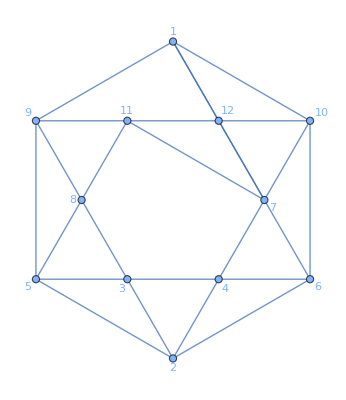
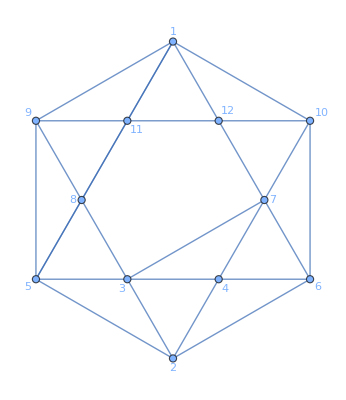
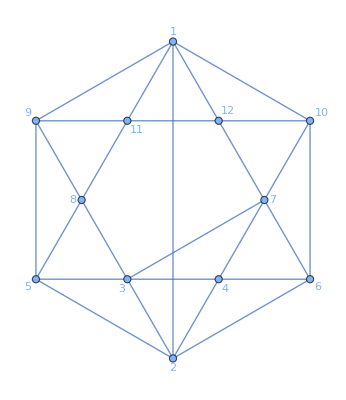
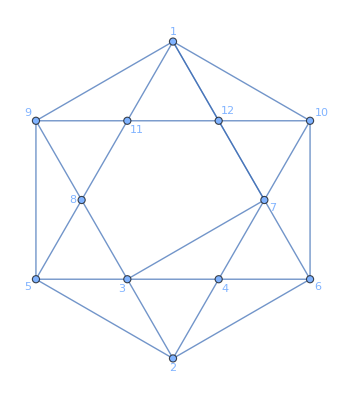
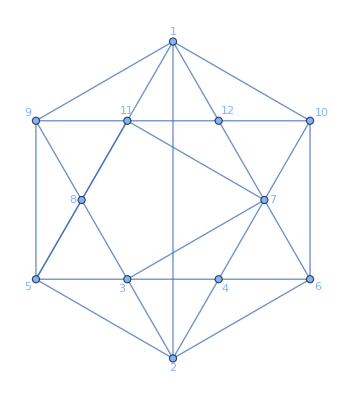
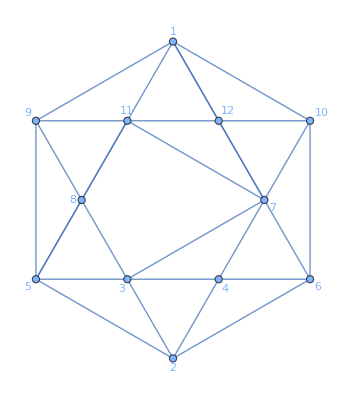
{-Graphics-
-5
1,-Graphics-
-1
x[5,7],-Graphics-
-1
x[2,7],-Graphics-
0
1,-Graphics-
0
x[1,3] x[5,7],-Graphics-
1
x[1,3] x[2,7],-Graphics-
-1
x[1,3],-Graphics-
0
x[1,3] x[2,7] x[5,7],-Graphics-
0
x[1,3] x[5,7],-Graphics-
0
x[1,3] x[2,7],-Graphics-
1
x[1,8] x[5,7],-Graphics-
0
x[1,8] x[2,7],-Graphics-
-1
x[1,8],-Graphics-
0
x[1,8] x[2,7] x[5,7],-Graphics-
0
x[1,8] x[5,7],-Graphics-
0
x[1,8] x[2,7],-Graphics-
0
x[1,3] x[1,8] x[2,7] x[5,7],-Graphics-
0
x[1,3] x[1,8] x[5,7],-Graphics-
0
x[1,3] x[1,8] x[2,7],-Graphics-
0
x[1,3] x[1,8] x[2,7] x[5,7]}

```mathematica
fGraphList[8][[1609]]
displayfgraph[%]
coords=GraphEmbedding[%[[1,1]]]
t1=%%%((x[7,#[[1]]]x[7,#[[2]]]x[7,#[[3]]]x[1,#[[4]]]x[1,#[[5]]]x[1,#[[6]]]&)/@(Join[#,Complement[{8,3,11,5,2,6},#]]&/@Subsets[{8,3,11,5,2,6},{3}]))/(x[7,8]x[7,3]x[7,11]x[1,5]x[1,2]x[1,6])/.x[a_,b_]:>x[b,a]/;(b<a);
canonicalizefgraph/@%;
Position[fGraphListcan[8],#]&/@%
%//Flatten
amplitudeCoefficients[8][[#]]&/@%
Graph[displayfgraph[#][[1,1]],VertexCoordinates->coords]&/@t1;
Column/@Transpose[{%,%%,Numerator/@t1}]
```

1/(x[1,9] x[1,10] x[1,11] x[1,12] x[2,3] x[2,4] x[2,5] x[2,6] x[3,4] x[3,5] x[3,8] x[4,6] x[4,7] x[5,8] x[5,9] x[6,7] x[6,10] x[7,10] x[7,12] x[8,9] x[8,11] x[9,11] x[10,12] x[11,12])

-Graphics-
1

{{-1.83697×10^-16,1.},{6.12323×10^-17,-1.},{-0.288675,-0.5},{0.288675,-0.5},{-0.866025,-0.5},{0.866025,-0.5},{0.57735,-8.9407×10^-8},{-0.57735,-1.78814×10^-7},{-0.866025,0.5},{0.866025,0.5},{-0.288675,0.5},{0.288675,0.5}}

{{{1609}},{{1757}},{{2528}},{{2175}},{{166}},{{2175}},{{261}},{{1667}},{{122}},{{261}},{{2571}},{{1757}},{{166}},{{2575}},{{2601}},{{1667}},{{2601}},{{262}},{{122}},{{2598}}}

{1609,1757,2528,2175,166,2175,261,1667,122,261,2571,1757,166,2575,2601,1667,2601,262,122,2598}

{-5,-1,1/2,0,0,0,0,0,-1,0,2,-1,0,-1/2,0,0,0,0,-1,0}

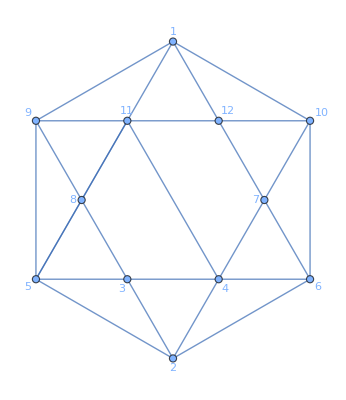
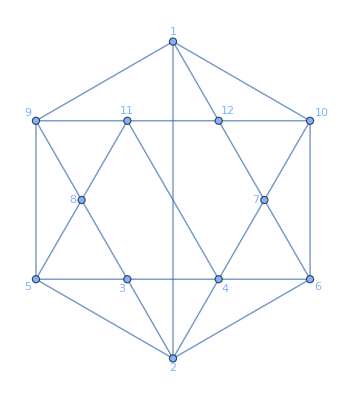
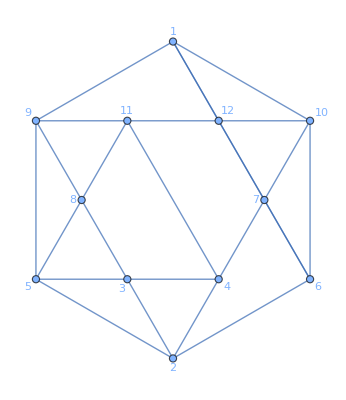
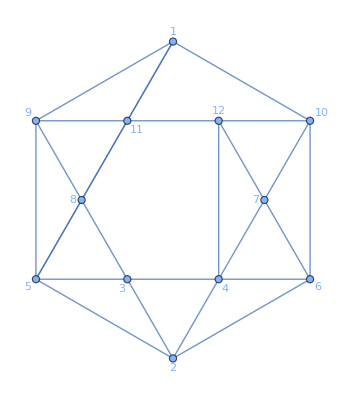
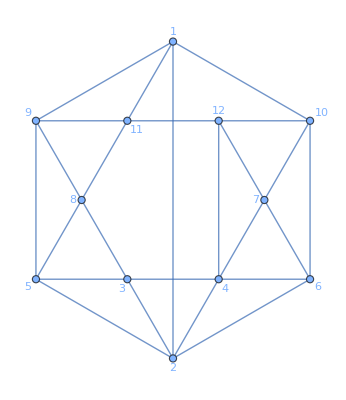
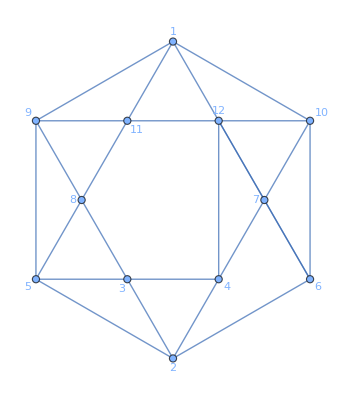
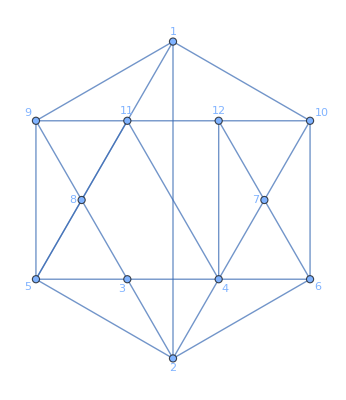
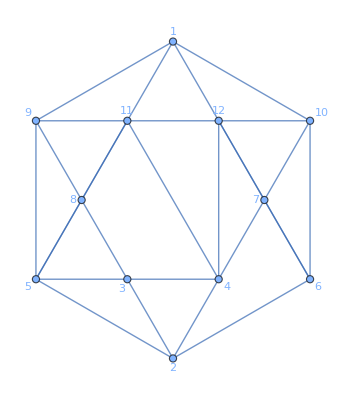
{-Graphics-
-5,-Graphics-
-1,-Graphics-
1/2,-Graphics-
0,-Graphics-
0,-Graphics-
0,-Graphics-
0,-Graphics-
0,-Graphics-
-1,-Graphics-
0,-Graphics-
2,-Graphics-
-1,-Graphics-
0,-Graphics-
-1/2,-Graphics-
0,-Graphics-
0,-Graphics-
0,-Graphics-
0,-Graphics-
-1,-Graphics-
0}

```mathematica
fGraphList[8][[1609]]
displayfgraph[%]
coords=GraphEmbedding[%[[1,1]]]
t1=%%%((x[4,#[[1]]]x[4,#[[2]]]x[4,#[[3]]]x[1,#[[4]]]x[1,#[[5]]]x[1,#[[6]]]&)/@(Join[#,Complement[{8,12,11,5,2,6},#]]&/@Subsets[{8,12,11,5,2,6},{3}]))/(x[4,8]x[4,12]x[4,11]x[1,5]x[1,2]x[1,6]);
canonicalizefgraph/@%;
Position[fGraphListcan[8],#]&/@%
%//Flatten
amplitudeCoefficients[8][[#]]&/@%
Graph[displayfgraph[#][[1,1]],VertexCoordinates->coords]&/@t1;
Column/@Transpose[{%,%%}]
```

```mathematica
(* Positions and coeffficents of 8 loop graphs with a t least two pentagonal faces *)
(Length/@orderedVertsToFaces[#])&/@planarGraphDials[8];
Position[%,_?(Count[#,5]>1&)]//Flatten
Table[dialnumtofnum[8,{#,ii}],{ii,1,Length[fGraphNums[8][[#]]]}]&/@%
%/.ad_Integer:>amplitudeCoefficients[8][[ad]]
```

{61,123,160,188,386,665,687,721,791,998,1014,1083,1104,1145,1147,1156,1227,1247,1305,1312,1317,1334,1392,1394,1396,1401,1404,1405,1406,1425,1426,1431}

{{166},{261},{302},{333},{692},{1608},{1650,1651},{1696,1697},{1788},{2122},{2150},{2254},{2276},{2325},{2327},{2337},{2442},{2469},{2556},{2564},{2571},{2598},{2663,2664},{2666},{2668},{2673},{2676},{2677},{2678},{2701},{2702},{2708}}

{{0},{0},{2},{0},{0},{0},{0,2},{0,2},{2},{-2},{0},{0},{0},{0},{0},{0},{2},{2},{2},{-1},{2},{0},{0,0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
fGraphList[4][[1]]/.x[5,6]x[7,8]->x[5,7]x[6,8]//canonicalizefgraph
Position[fGraphListcan[4],%]
fGraphList[4][[1]]/.x[5,6]x[7,8]->x[5,8]x[6,7]//canonicalizefgraph
Position[fGraphListcan[4],%]
graphSymmetryFactor[%%]
graphSymmetryFactor[#]&/@fGraphList[4]
```

1/(x[1,2] x[1,3] x[1,4] x[1,6] x[2,3] x[2,5] x[2,7] x[3,6] x[3,7] x[4,5] x[4,6] x[4,8] x[5,7] x[5,8] x[6,8] x[7,8])

{{2}}

1/(x[1,2] x[1,3] x[1,4] x[1,6] x[2,3] x[2,5] x[2,7] x[3,6] x[3,7] x[4,5] x[4,6] x[4,8] x[5,7] x[5,8] x[6,8] x[7,8])

{{2}}

16

{8,16,24}

```mathematica
canonicalizefgraph/@(fGraphList[4][[1]]/.(x[5,6] x[7,8] )->(x[#[[1]],#[[2]]] x[#[[3]],#[[4]]] &/@Permutations[{5,6,7,8}]))
Position[fGraphListcan[4],#]&/@%//Flatten
amplitudeCoefficients[4][[#]]&/@%
graphSymmetryFactor[#]&/@%%%
24 %%/%
Total[%]
```

{(x[5,6] x[7,8])/(x[1,2] x[1,5] x[1,6] x[1,7] x[2,5] x[2,6] x[2,8] x[3,4] x[3,5] x[3,7] x[3,8] x[4,6] x[4,7] x[4,8] x[5,7] x[5,8] x[6,7] x[6,8]),(x[5,6] x[7,8])/(x[1,2] x[1,5] x[1,6] x[1,7] x[2,5] x[2,6] x[2,8] x[3,4] x[3,5] x[3,7] x[3,8] x[4,6] x[4,7] x[4,8] x[5,7] x[5,8] x[6,7] x[6,8]),1/(x[1,2] x[1,3] x[1,4] x[1,6] x[2,3] x[2,5] x[2,7] x[3,6] x[3,7] x[4,5] x[4,6] x[4,8] x[5,7] x[5,8] x[6,8] x[7,8]),1/(x[1,2] x[1,3] x[1,4] x[1,6] x[2,3] x[2,5] x[2,7] x[3,6] x[3,7] x[4,5] x[4,6] x[4,8] x[5,7] x[5,8] x[6,8] x[7,8]),1/(x[1,2] x[1,3] x[1,4] x[1,6] x[2,3] x[2,5] x[2,7] x[3,6] x[3,7] x[4,5] x[4,6] x[4,8] x[5,7] x[5,8] x[6,8] x[7,8]),1/(x[1,2] x[1,3] x[1,4] x[1,6] x[2,3] x[2,5] x[2,7] x[3,6] x[3,7] x[4,5] x[4,6] x[4,8] x[5,7] x[5,8] x[6,8] x[7,8]),(x[5,6] x[7,8])/(x[1,2] x[1,5] x[1,6] x[1,7] x[2,5] x[2,6] x[2,8] x[3,4] x[3,5] x[3,7] x[3,8] x[4,6] x[4,7] x[4,8] x[5,7] x[5,8] x[6,7] x[6,8]),(x[5,6] x[7,8])/(x[1,2] x[1,5] x[1,6] x[1,7] x[2,5] x[2,6] x[2,8] x[3,4] x[3,5] x[3,7] x[3,8] x[4,6] x[4,7] x[4,8] x[5,7] x[5,8] x[6,7] x[6,8]),1/(x[1,2] x[1,3] x[1,4] x[1,6] x[2,3] x[2,5] x[2,7] x[3,6] x[3,7] x[4,5] x[4,6] x[4,8] x[5,7] x[5,8] x[6,8] x[7,8]),1/(x[1,2] x[1,3] x[1,4] x[1,6] x[2,3] x[2,5] x[2,7] x[3,6] x[3,7] x[4,5] x[4,6] x[4,8] x[5,7] x[5,8] x[6,8] x[7,8]),1/(x[1,2] x[1,3] x[1,4] x[1,6] x[2,3] x[2,5] x[2,7] x[3,6] x[3,7] x[4,5] x[4,6] x[4,8] x[5,7] x[5,8] x[6,8] x[7,8]),1/(x[1,2] x[1,3] x[1,4] x[1,6] x[2,3] x[2,5] x[2,7] x[3,6] x[3,7] x[4,5] x[4,6] x[4,8] x[5,7] x[5,8] x[6,8] x[7,8]),1/(x[1,2] x[1,3] x[1,4] x[1,6] x[2,3] x[2,5] x[2,7] x[3,6] x[3,7] x[4,5] x[4,6] x[4,8] x[5,7] x[5,8] x[6,8] x[7,8]),1/(x[1,2] x[1,3] x[1,4] x[1,6] x[2,3] x[2,5] x[2,7] x[3,6] x[3,7] x[4,5] x[4,6] x[4,8] x[5,7] x[5,8] x[6,8] x[7,8]),1/(x[1,2] x[1,3] x[1,4] x[1,6] x[2,3] x[2,5] x[2,7] x[3,6] x[3,7] x[4,5] x[4,6] x[4,8] x[5,7] x[5,8] x[6,8] x[7,8]),1/(x[1,2] x[1,3] x[1,4] x[1,6] x[2,3] x[2,5] x[2,7] x[3,6] x[3,7] x[4,5] x[4,6] x[4,8] x[5,7] x[5,8] x[6,8] x[7,8]),(x[5,6] x[7,8])/(x[1,2] x[1,5] x[1,6] x[1,7] x[2,5] x[2,6] x[2,8] x[3,4] x[3,5] x[3,7] x[3,8] x[4,6] x[4,7] x[4,8] x[5,7] x[5,8] x[6,7] x[6,8]),(x[5,6] x[7,8])/(x[1,2] x[1,5] x[1,6] x[1,7] x[2,5] x[2,6] x[2,8] x[3,4] x[3,5] x[3,7] x[3,8] x[4,6] x[4,7] x[4,8] x[5,7] x[5,8] x[6,7] x[6,8]),1/(x[1,2] x[1,3] x[1,4] x[1,6] x[2,3] x[2,5] x[2,7] x[3,6] x[3,7] x[4,5] x[4,6] x[4,8] x[5,7] x[5,8] x[6,8] x[7,8]),1/(x[1,2] x[1,3] x[1,4] x[1,6] x[2,3] x[2,5] x[2,7] x[3,6] x[3,7] x[4,5] x[4,6] x[4,8] x[5,7] x[5,8] x[6,8] x[7,8]),1/(x[1,2] x[1,3] x[1,4] x[1,6] x[2,3] x[2,5] x[2,7] x[3,6] x[3,7] x[4,5] x[4,6] x[4,8] x[5,7] x[5,8] x[6,8] x[7,8]),1/(x[1,2] x[1,3] x[1,4] x[1,6] x[2,3] x[2,5] x[2,7] x[3,6] x[3,7] x[4,5] x[4,6] x[4,8] x[5,7] x[5,8] x[6,8] x[7,8]),(x[5,6] x[7,8])/(x[1,2] x[1,5] x[1,6] x[1,7] x[2,5] x[2,6] x[2,8] x[3,4] x[3,5] x[3,7] x[3,8] x[4,6] x[4,7] x[4,8] x[5,7] x[5,8] x[6,7] x[6,8]),(x[5,6] x[7,8])/(x[1,2] x[1,5] x[1,6] x[1,7] x[2,5] x[2,6] x[2,8] x[3,4] x[3,5] x[3,7] x[3,8] x[4,6] x[4,7] x[4,8] x[5,7] x[5,8] x[6,7] x[6,8])}

{1,1,2,2,2,2,1,1,2,2,2,2,2,2,2,2,1,1,2,2,2,2,1,1}

{1,1,-1,-1,-1,-1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,-1,-1,-1,-1,1,1}

{8,8,16,16,16,16,8,8,16,16,16,16,16,16,16,16,8,8,16,16,16,16,8,8}

{3,3,-3/2,-3/2,-3/2,-3/2,3,3,-3/2,-3/2,-3/2,-3/2,-3/2,-3/2,-3/2,-3/2,3,3,-3/2,-3/2,-3/2,-3/2,3,3}

0

```mathematica
canonicalizefgraph/@(fGraphList[5][[1]]/.(x[4,6] x[5,8] x[7,9])->(x[#[[1]],#[[2]]] x[#[[3]],#[[4]]] x[#[[5]],#[[6]]]&/@Permutations[{4,6,5,8,7,9}]))//Union;
Position[fGraphListcan[5],#]&/@%//Flatten
amplitudeCoefficients[5][[#]]&/@%
graphSymmetryFactor[#]&/@%%%
24 %%/%
Total[%]
```

{7,1,2,5}

{1,1,-1,-1}

{12,6,8,2}

{2,4,-3,-12}

-9

#### The coefficients of graphs involved in relation to anti-prism graphs as given in https://arxiv.org/pdf/2503.15593

```mathematica
expre[m_]:=(-1)^(m+Sum[p[k,k],{k,1,m}])Product[cc[p[1,k]-q[m-k+2,m]-3]cc[q[m-k+1,m]-p[1,k]],{k,1,m}]
```

```mathematica
p[i_,j_]:=x[j]-x[i-1]+2(j-i+1)
q[i_,j_]:=y[j]-y[i-1]+2(j-i+1)
```

```mathematica
y[k_]:=n-yp[m-k]+2
```

```mathematica
cc[p[1,k]-q[m-k+2,m]-3]cc[q[m-k+1,m]-p[1,k]]/.x[0]->2/.yp[0]->2//Simplify
```

cc[-1+x[k]-yp[-1+k]] cc[-x[k]+yp[k]]

```mathematica
expre[1]/.x[0]->2/.m->1/.yp[0]->2/.x[1]->n/.yp[1]->n
```

(-1)^(1+n) cc[0] cc[-3+n]

```mathematica
expre[5]/.m->5/.x[i_]->i+2/.yp[i_]->i+2
```

cc[0]^10

```mathematica
expre[2]
%/.{p[i_,j_]:>Sum[p[k],{k,i,j}],q[i_,j_]:>Sum[q[k],{k,i,j}]}
%/.{p[1]->4,p[2]->3,q[1]->4,q[2]->3}
```

(-1)^(2+p[1]+p[2]) cc[-p[1,2]+q[1,2]] cc[-3+p[1,2]-q[2,2]] cc[-p[1,1]+q[2,2]] cc[-3+p[1,1]-q[3,2]]

(-1)^(2+p[1]+p[2]) cc[-3+p[1]] cc[-3+p[1]+p[2]-q[2]] cc[-p[1]+q[2]] cc[-p[1]-p[2]+q[1]+q[2]]

-cc[-1] cc[0] cc[1]^2